```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SLattice/peak_theory

```mathematica
<<init`
```

## Peak Theory LN

```mathematica
calPg[lnk_,s2_]=Ag/Sqrt[2π s2] Exp[(-(lnk-lnks)^2)/(2s2)];
```

```mathematica
σn2[n_,s2_]=Ag E^(2 n^2 s2)ks^(2n);
```

```mathematica
Rn[n_,s2_]=Simplify[Sqrt[3 σn2[n,s2]/σn2[n+1,s2]],{s2>0,n>0,ks>0}]
```

(√3 ⅇ^(-((1+2 n) s2)))/ks

```mathematica
γn[s2_]=Simplify[σn2[n,s2]/Sqrt[σn2[n-1,s2]σn2[n+1,s2]],{ks>0,n>0,s2>0,Ag>0}]
```

ⅇ^(-2 s2)

```mathematica
ζ[x_,k3t_,s2_]=Simplify[σn2[1,s2]/Sqrt[σn2[2,s2]] ν2(1/(1-γn[s2]^2)(ψ1[x,s2]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2[x,s2])-k3t^2/(γn[s2](1-γn[s2]^2))(γn[s2]^2 ψ1[x,s2]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2[x,s2])),{s2>0,ks>0}]
```

(√Ag ⅇ^(-6 s2) ν2 (ⅇ^(6 s2) (ⅇ^(2 s2)-k3t^2) ψ1[x,s2]+(-1+ⅇ^(2 s2) k3t^2) ψ2[x,s2]))/(-1+ⅇ^(4 s2))

```mathematica
ψn[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^(2n lnk)calPg[lnk,s2]Sinc[E^lnk x]/.{lnks->0}],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnp[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^((2n +1)lnk)calPg[lnk,s2]Sinc'[E^lnk x]/.{lnks->0}],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnpp[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^((2n +2)lnk)calPg[lnk,s2]Sinc''[E^lnk x]/.{lnks->0}],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
s2s=10^-2;
AbsoluteTiming[
ψ1List=ParallelTable[{x,ψn[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ1pList=ParallelTable[{x,ψnp[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ1ppList=ParallelTable[{x,ψnpp[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψn[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψnp[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ2ppList=ParallelTable[{x,ψnpp[x,2,s2s]},{x,10^-2,10,10^-2}];]
```

{27.4191,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ1ppint[x_]=Interpolation[ψ1ppList][x];
ψ2int[x_]=Interpolation[ψ2List][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
ψ2ppint[x_]=Interpolation[ψ2ppList][x];
```

```mathematica
ζx[x_,k3t_]=Simplify[(1/(1-γn[s2]^2)(ψ1int[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2int[x])-k3t^2/(γn[s2](1-γn[s2]^2))(γn[s2]^2 ψ1int[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2int[x]))/.{s2->s2s}];
ζp[x_,k3t_]=Simplify[(1/(1-γn[s2]^2)(ψ1pint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2pint[x])-k3t^2/(γn[s2](1-γn[s2]^2))(γn[s2]^2 ψ1pint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2pint[x]))/.{s2->s2s}];
ζpp[x_,k3t_]=Simplify[(1/(1-γn[s2]^2)(ψ1ppint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2ppint[x])-k3t^2/(γn[s2](1-γn[s2]^2))(γn[s2]^2 ψ1ppint[x]-1/3 Rn[3,s2]^2 σn2[2,s2]/σn2[1,s2] ψ2ppint[x]))/.{s2->s2s}];
```

```mathematica
CmCond[x_,k3t_]=(ζp[x,k3t]+x ζpp[x,k3t])/x^3//Simplify
```

1/((-1+ⅇ^(1/25)) ⅇ^(1/25) x^3)((-1+ⅇ^(1/50) k3t^2) x InterpolatingFunction[…][x]+ⅇ^(3/50) (ⅇ^(1/50)-k3t^2) x InterpolatingFunction[…][x]+(-1+ⅇ^(1/50) k3t^2) InterpolatingFunction[…][x]+ⅇ^(3/50) (ⅇ^(1/50)-k3t^2) InterpolatingFunction[…][x])

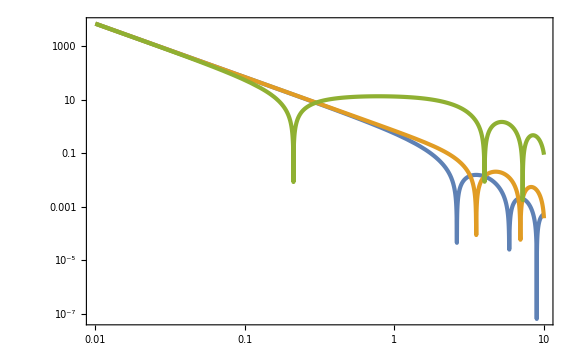

```mathematica
LogLogPlot[{Abs[CmCond[x,1]],Abs[CmCond[x,10^-2]],Abs[CmCond[x,10]]},{x,10^-2,10}]
```

```mathematica
xmList=ParallelTable[{k3t,x/.FindRoot[CmCond[x,k3t]==0,{x,Min[1/(2 k3t),1]},WorkingPrecision->30]//Quiet},{k3t,10^-2,10,10^-2}];
```

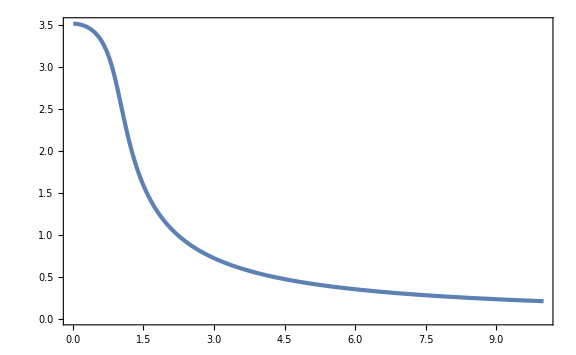

```mathematica
ListPlot[xmList,PlotRange->Full]
```

```mathematica
xmint[k3t_]=Interpolation[xmList][k3t];
```

```mathematica
Cm[ν2_,k3t_,Ag_]=Simplify[2/3(1-(1+xmint[k3t] σn2[1,s2s]/Sqrt[σn2[2,s2s]] ν2 ζp[xmint[k3t],k3t])^2),{Ag>0,ks>0}];
```

```mathematica
Cth=533/1000(*45/100*);
As=5 10^-3;
npeak=16;
nbias=16;
NL=256;
kpeak=(2π npeak)/NL
```

π/8

π/8

π/8

```mathematica
mukdata=Import["data/LN_muk_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_GB.csv"];
Ntot=Length[mukdata]
```

994

```mathematica
Map[(#[[4]])/(#[[3]])&,mukdata][[1;;50]]
```

{6.,5.00001,5.99999,6.,6.,6.00001,6.,5.,5.,5.,5.00001,6.,4.99999,6.,6.00001,5.,5.,7.,6.00001,6.,6.00001,5.,6.,6.00001,6.,4.99999,6.00001,5.00001,5.00001,5.,5.,6.,5.99999,5.00001,4.99999,5.00001,5.,6.,6.,5.99999,6.,6.,5.99999,5.,6.,5.,6.00001,6.,6.,6.}

```mathematica
rm=2.7/kpeak
```

6.87549

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
```

```mathematica
Cratio=Map[Cm[(#[[2]])/σ2,Sqrt[σ2/σ4]#[[3]],As]/(#[[6]])/.{s2->s2s}&,mukdata];
```

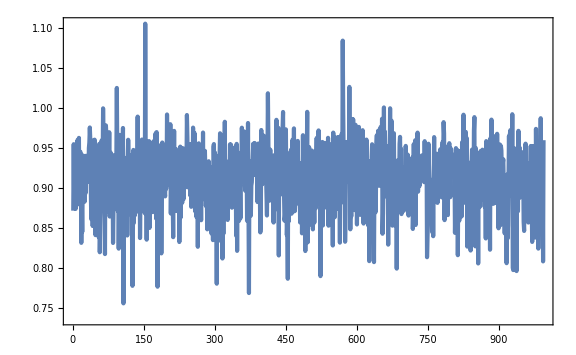

```mathematica
ListPlot[Cratio]
```

```mathematica
k3tvsxm=Map[{Sqrt[σ2/σ4]#[[3]]/.{s2->s2s},kpeak(#[[4]])/(#[[3]])}&,mukdata];
```

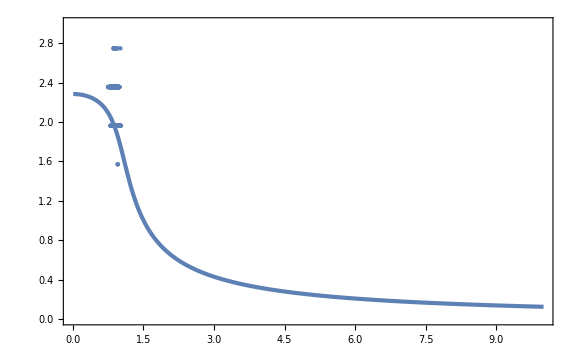

```mathematica
Show[ListPlot[xmList,PlotRange->{0,3}],ListPlot[k3tvsxm,Joined->False]]
```

```mathematica
xmvsCr=Map[{kpeak(#[[4]])/(#[[3]]),Cm[(#[[2]])/σ2,Sqrt[σ2/σ4]#[[3]],As]/(#[[6]])/.{s2->s2s}}&,mukdata];
```

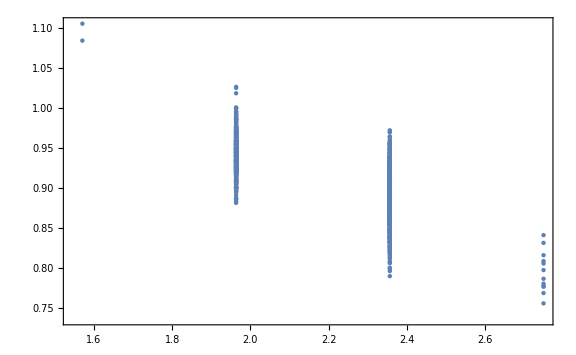

```mathematica
ListPlot[xmvsCr,Joined->False]
```

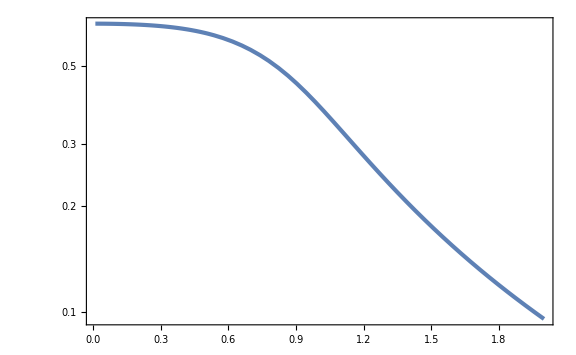

```mathematica
LogPlot[Cm[5,k3t,As],{k3t,10^-2,2},GridLines->{None,{Cth}}]
```

```mathematica
nuvsCm=Map[{(#[[2]])/σ2/.{s2->s2s},#[[6]]}&,mukdata];
```

```mathematica
k3tmean=Mean[Map[Sqrt[σ2/σ4]#[[3]]/.{s2->s2s}&,mukdata]]
```

0.900219

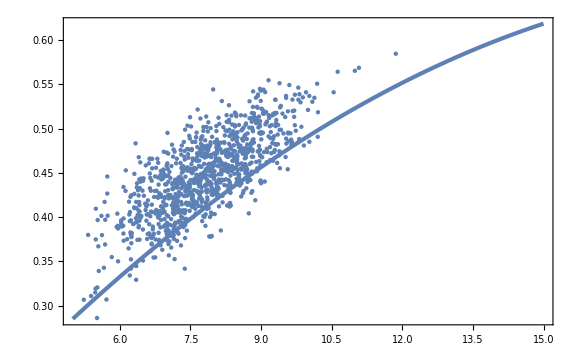

```mathematica
Show[Plot[Cm[nu2,k3tmean,As],{nu2,5,15},GridLines->{None,{Cth}}],ListPlot[nuvsCm,Joined->False]]
```

```mathematica
FindMaximum[{Cm[nu2,10^-2,As],5<=nu2<=15},{nu2,10}]
FindMaximum[{Cm[nu2,10,As],5<=nu2<=15},{nu2,10}]
```

{0.666667,{nu2→10.7597}}

{0.00531365,{nu2→15.}}

```mathematica
CmMList=Table[{k3t,FindMaximum[{Cm[nu2,k3t,As],5<=nu2<=15},{nu2,10},WorkingPrecision->30][[1]]},{k3t,10^-2,10,10^-2}];
```

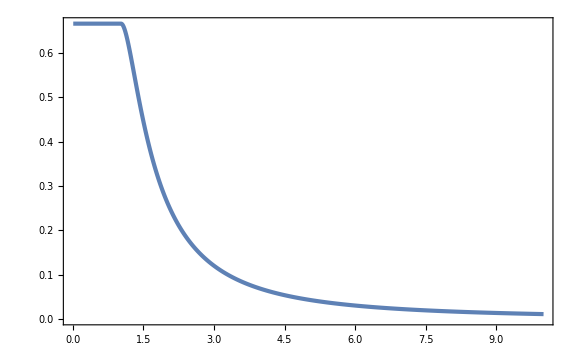

```mathematica
ListPlot[CmMList,GridLines->{None,{Cth}},PlotRange->Full]
```

```mathematica
CmMint[k3t_]=Interpolation[CmMList][k3t];
```

```mathematica
k3tMax=k3t/.FindRoot[CmMint[k3t]==Cth,{k3t,3/2},WorkingPrecision->30]
```

1.33798944407482789827129346964

```mathematica
nu2thList=Table[{k3t,nu2/.FindRoot[Cm[nu2,k3t,As]==Cth,{nu2,5},WorkingPrecision->30]},{k3t,10^-2,k3tMax,10^-2}];
```

FindRoot::precw: The precision of the argument function (2/3 (1-(1-0.178836242849999753521363085 nu2)^2)==533/1000) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (2/3 (1-(1-0.178796932813122161656700629 nu2)^2)==533/1000) is less than WorkingPrecision (30.).

FindRoot::precw: The precision of the argument function (2/3 (1-(1-0.178731419923464289896178149 nu2)^2)==533/1000) is less than WorkingPrecision (30.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

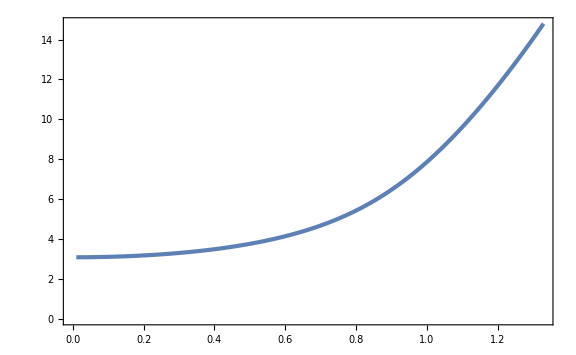

```mathematica
ListPlot[nu2thList]
```

```mathematica
nu2thint[k3t_]=Interpolation[nu2thList][k3t];
```

```mathematica
MPBH[nu2_,k3t_]=Simplify[xmint[k3t]^2 E^(2 σn2[1,s2s]/Sqrt[σn2[2,s2s]] nu2 ζx[xmint[k3t],k3t])(Cm[nu2,k3t,As]-Cth)^γ/.{γ->36/100,Ag->As(*,Cth->0.533*)},{ks>0}];
dlnMdnu2[nu2_,k3t_]=D[Log[MPBH[nu2,k3t]], nu2];
```

```mathematica
seeds="0";
s2value="0,01";
Cdata=Import["data/LN_compaction_"<>s2value<>"_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_"<>seeds<>".csv"];
```

```mathematica
mu2data=Last[Cdata][[1]];
k3data=Last[Cdata][[2]];
xmdata=Last[Cdata][[3]];
zetamdata=Last[Cdata][[4]];
Cmdata=Max[Drop[Cdata,-1][[All,2]]];
nu2data=mu2data/σ2/.{s2->s2s};
k3tdata=Sqrt[σ2/σ4]k3data/.{s2->s2s};
```

```mathematica
xmdata
xmint[k3tdata]
```

2.74889

2.6893

```mathematica
Cmdata
Cm[nu2data,k3tdata,As]
```

0.577697

0.574581

```mathematica
zetamdata
Simplify[σn2[1,s2s]/Sqrt[σn2[2,s2s]] nu2data ζx[xmint[k3tdata],k3tdata]/.{Ag->As},{ks>0}]
```

0.0934977

0.0965056

```mathematica
MPBH[nu2data,k3tdata]
xmdata^2 E^(2 zetamdata^2)(Cmdata-Cth)^γ/.{γ->0.36}
```

2.79192

2.51193

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γn[s2s]^2])Exp[-1/2(ν^2+(ξ-γn[s2s] ν)^2/(1-γn[s2s]^2))];
npkPT[nu2_,k3t_,ks_]=Simplify[2/(6π)^(3/2)Sqrt[σn2[4,s2s]/σn2[3,s2s]]^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2],{ks>0}];
```

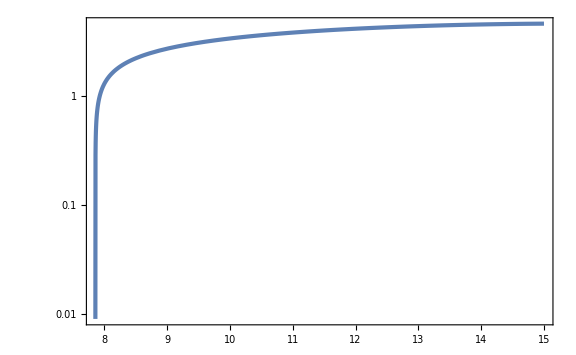

```mathematica
LogPlot[MPBH[nu2,1],{nu2,nu2thint[1],15},PlotRange->Full]
```

```mathematica
FindMaximum[{MPBH[nu2,1],nu2thint[1]<nu2<15},{nu2,(nu2thint[1]+15)/2}]
```

{4.5718,{nu2→15.}}

```mathematica
MPBHMList=Table[{k3t,FindMaximum[{MPBH[nu2,k3t],nu2thint[k3t]<nu2<15},{nu2,(3nu2thint[k3t]+15)/4},WorkingPrecision->30][[1]]},{k3t,10^-2,k3tMax,10^-2}];
```

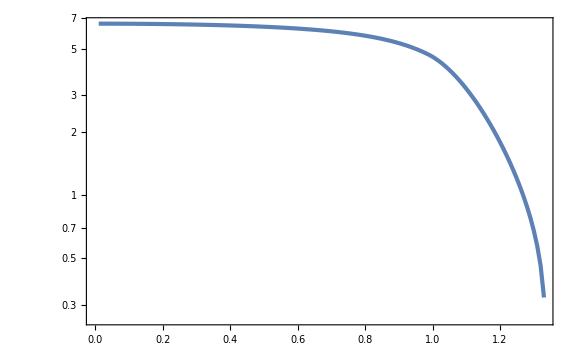

```mathematica
ListLogPlot[MPBHMList]
```

```mathematica
MPBHMint[k3t_]=Interpolation[MPBHMList][k3t];
k3tMint[M_]:=Interpolation[RotateRight[MPBHMList,{0,1}]][M]/;M>Last[MPBHMList][[2]]
k3tMint[M_]:=Last[MPBHMList][[1]]/;M<=Last[MPBHMList][[2]]
```

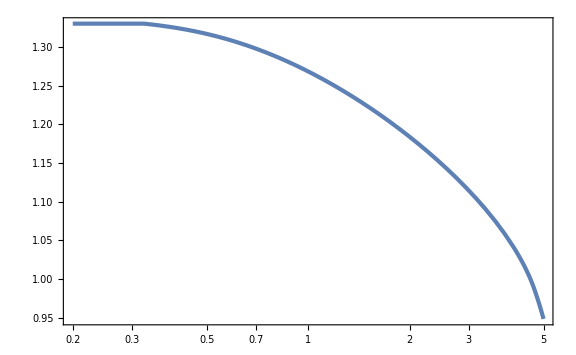

```mathematica
LogLinearPlot[k3tMint[M],{M,0.2,5}]
```

```mathematica
nu2inMk3tList=Flatten[ParallelTable[{M,k3t,nu2/.FindRoot[MPBH[nu2,k3t]==M,{nu2,nu2thint[k3t]+10^-2,nu2thint[k3t],16},WorkingPrecision->30]//Quiet},{M,2/10,5,10^-2},{k3t,10^-2,k3tMint[M],(k3tMint[M]-10^-2)/100}],1];//AbsoluteTiming
```

{36.7688,Null}

```mathematica
nu2int[M_,k3t_]=Interpolation[nu2inMk3tList][M,k3t];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

```mathematica
ListContourPlot[nu2inMk3tList]
```

-Graphics-

```mathematica
nPBH[M_]:=NIntegrate[npkPT[nu2int[M,k3t],k3t,kpeak]/Abs[dlnMdnu2[nu2int[M,k3t],k3t]],{k3t,10^-2,k3tMint[M]}]
```

```mathematica
nPBHList=ParallelTable[{M,nPBH[M]},{M,2/10,5,10^-2}];//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{777.781,Null}

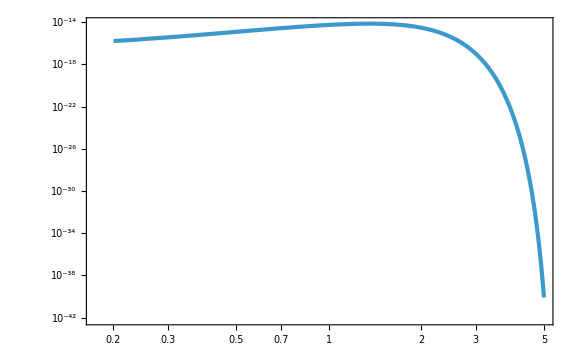

```mathematica
ListLogLogPlot[nPBHList]
```

```mathematica
Export["data/nPBH_LN_0,01_PT.csv",nPBHList//N];
```

```mathematica
ListLogLogPlot[Import["data/nPBH_LN_0,01_PT.csv"]]
```

-Graphics-

## Peak Theory scale-inv.

### Laplacian peak

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,mu>0,kappa>0,n^2-1>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
psin[n_,r_,kW_]=1/sigman[n,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2]

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(2-2 Cos[kW r])/(kW^2 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamman[n_]=sigman[n,kW,As]^2/(sigman[n-1,kW,As]sigman[n+1,kW,As])//Simplify
Rn[n_,kW_]=√3 sigman[n,kW,As]/sigman[n+1,kW,As]//Simplify
```

(√(-1+n^2))/n

(√(3+3/n))/kW

```mathematica
1/x^2 D[(x^2 D[psin[1,x,kW], x]), x]+(sigman[2,kW,As]/sigman[1,kW,As])^2 psin[2,x,kW]//Simplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[2,x,kW], x]), x]+(sigman[3,kW,As]/sigman[2,kW,As])^2 psin[3,x,kW]//Simplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[3,x,kW], x]), x]+(sigman[4,kW,As]/sigman[3,kW,As])^2 psin[4,x,kW]//Simplify
```

0

```mathematica
zetax[x_,mu2_,kappa_]=mu2(1/(1-gamman[3]^2)(psin[1,x/kW,kW]-1/3 Rn[3,kW]^2 sigman[2,kW,As]^2/sigman[1,kW,As]^2 psin[2,x/kW,kW])-kappa^2/(gamman[3](1-gamman[3]^2))(gamman[3]^2 psin[1,x/kW,kW]-1/3 Rn[3,kW]^2 sigman[2,kW,As]^2/sigman[1,kW,As]^2 psin[2,x/kW,kW]))//Simplify
```

-(6 mu2 (-8+6 √2 kappa^2-3 x^2+2 √2 kappa^2 x^2+(8-x^2+√2 kappa^2 (-6+x^2)) Cos[x]-2 (-4+3 √2 kappa^2) x Sin[x]))/x^4

```mathematica
zetaLap[x_,mu_,kappa_]=1/x^2 D[(x^2 D[zetax[x,mu,kappa], x]), x]//Simplify
```

1/x^6 6 mu (96-72 √2 kappa^2+6 x^2-4 √2 kappa^2 x^2+(-96+42 x^2-x^4+√2 kappa^2 (72-32 x^2+x^4)) Cos[x]-2 x (48-5 x^2+4 √2 kappa^2 (-9+x^2)) Sin[x])

```mathematica
Normal[Series[-kW^2 zetaLap[x,mu,kappa](sigman[1,kW,As]/sigman[2,kW,As])^2,{x,0,1}]]
```

mu

```mathematica
zetaLL[x_,mu_,kappa_]=1/x^2 D[(x^2 D[zetaLap[x,mu,kappa], x]), x]//Simplify
```

-1/x^8 6 mu (-72 (40+x^2)+48 √2 kappa^2 (45+x^2)+(2880-1368 x^2+84 x^4-x^6+√2 kappa^2 (-2160+1032 x^2-66 x^4+x^6)) Cos[x]-2 x (-6 (240-34 x^2+x^4)+√2 kappa^2 (1080-156 x^2+5 x^4)) Sin[x])

```mathematica
Normal[Series[kW^4 zetaLL[x,mu,kappa]/mu(sigman[1,kW,As]/sigman[2,kW,As])^2 sigman[2,kW,As]/sigman[4,kW,As],{x,0,1}]]
```

kappa^2

```mathematica
CompactC[x_,mu_,kappa_]=(1-(1+x D[zetax[x,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-1/x^8(-192 mu+144 √2 kappa^2 mu-36 mu x^2+24 √2 kappa^2 mu x^2+x^4+12 mu (16-5 x^2+4 √2 kappa^2 (-3+x^2)) Cos[x]+6 mu x (32-x^2+√2 kappa^2 (-24+x^2)) Sin[x])^2)

```mathematica
xmcond[x_,kappa_]=(D[zetax[x,mu,kappa], x]+x D[D[zetax[x,mu,kappa], x], x])x^5/(12mu)//Simplify
```

64-48 √2 kappa^2+6 x^2-4 √2 kappa^2 x^2+1/2 (-128+52 x^2-x^4+√2 kappa^2 (96-40 x^2+x^4)) Cos[x]-1/2 x (128-11 x^2+3 √2 kappa^2 (-32+3 x^2)) Sin[x]

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->50]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.6592083883523112147945417748657759700612077960189

5.3701421552991077958189118888035944434174892377781

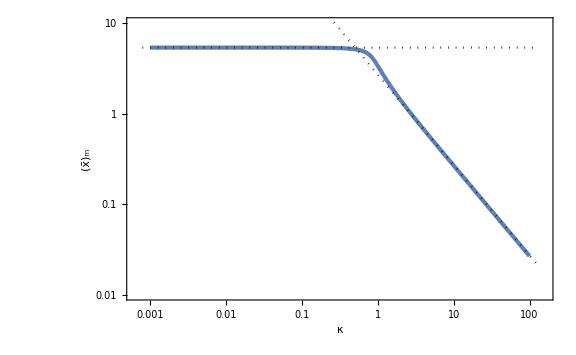

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.7/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==267/1000,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

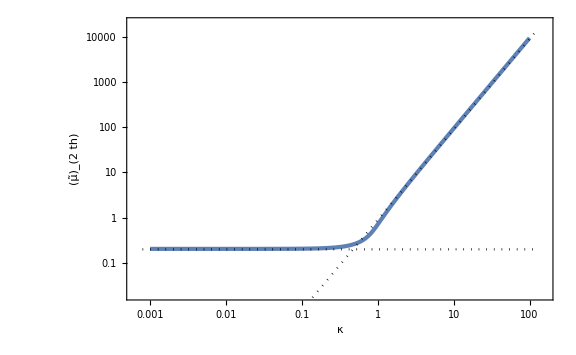

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.2,0.9 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

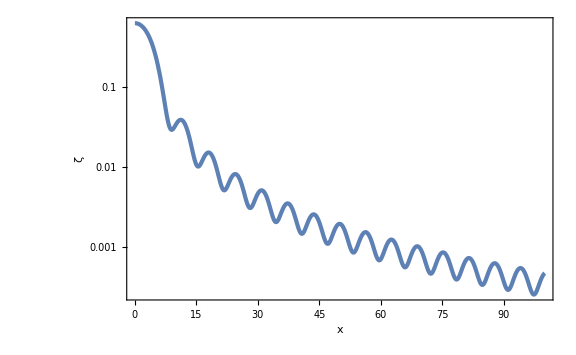

```mathematica
LogPlot[zetax[x,muthint[k],k]/.{k->0.1},{x,0.01,100},PlotRange->Full,FrameLabel->{x,ζ}]
```

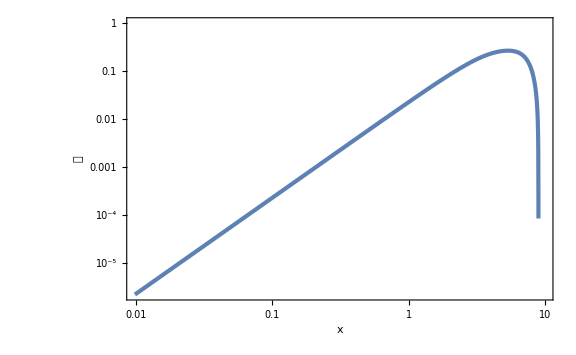

```mathematica
LogLogPlot[CompactC[x,muthint[k],k]/.{k->10^-1},{x,0,10},WorkingPrecision->50,FrameLabel->{x,𝒞}]
```

```mathematica
muthint[10]
```

93.716374899296789123751056186879802506929152269

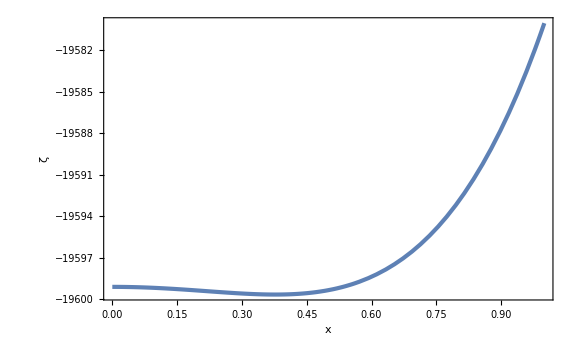

```mathematica
Plot[zetax[x,muthint[k],k]/.{k->10},{x,0,1},WorkingPrecision->50,FrameLabel->{x,ζ}]
```

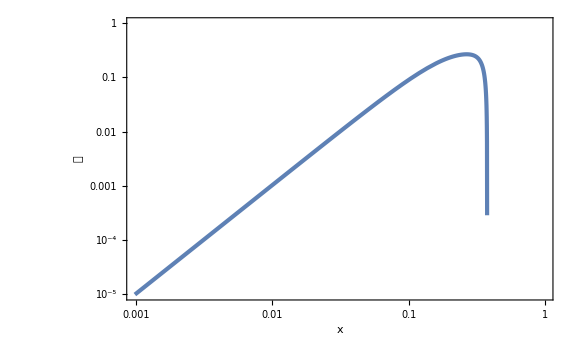

```mathematica
LogLogPlot[CompactC[x,muthint[k],k]/.{k->10},{x,0,1},WorkingPrecision->50,FrameLabel->{x,𝒞}]
```

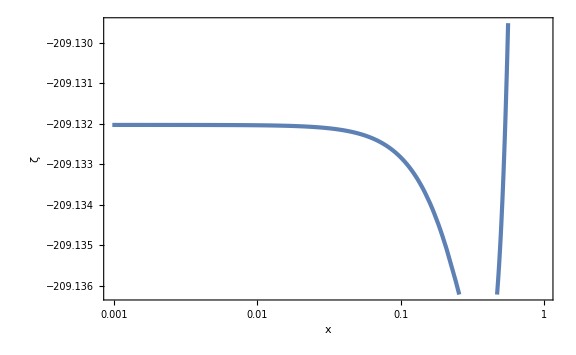

```mathematica
LogLinearPlot[zetax[x,1,k]/.{k->10},{x,0,1},WorkingPrecision->50,FrameLabel->{x,ζ}]
```

```mathematica
Normal[Series[-zetaLap[x,1,100](sigman[1,1,As]/sigman[2,1,As])^2,{x,0,1}]]
```

1

### direct peak

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kUV>0,kIR>0,kUV>kIR,mu>0,kappa>0,n^2-1>0,alpha>0,alpha<1};
```

```mathematica
sigman[n_,kUV_,kIR_,As_]=√(As Integrate[Exp[2n logk],{logk,Log[kIR],Log[kUV]}])//Simplify
```

(√((As (-kIR^(2 n)+kUV^(2 n)))/n))/(√2)

```mathematica
sigma0[kUV_,kIR_,As_]=√(As Integrate[1,{logk,Log[kIR],Log[kUV]}])//Simplify
```

√(As Log[kUV/kIR])

```mathematica
psin[n_,r_,kUV_,kIR_]=1/sigman[n,kUV,kIR,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,kIR,kUV}]//Simplify
psi0[r_,kUV_,kIR_]=1/sigma0[kUV,kIR,As]^2 As Integrate[Sin[k r]/(k r)1/k,{k,kIR,kUV}]//Simplify
```

-1/((-kIR^(2 n)+kUV^(2 n)) r)ⅈ n (kIR^(-1+2 n) (ExpIntegralE[2-2 n,-ⅈ kIR r]-ExpIntegralE[2-2 n,ⅈ kIR r])+kUV^(-1+2 n) (-ExpIntegralE[2-2 n,-ⅈ kUV r]+ExpIntegralE[2-2 n,ⅈ kUV r]))

(-r CosIntegral[kIR r]+r CosIntegral[kUV r]+Sin[kIR r]/kIR-Sin[kUV r]/kUV)/(r Log[kUV/kIR])

```mathematica
psin[1,r,kUV,kIR]//FullSimplify
psin[2,r,kUV,kIR]//FullSimplify
```

-(2 (Cos[kIR r]-Cos[kUV r]))/((kIR^2-kUV^2) r^2)

1/((kIR^4-kUV^4) r)2 ⅈ (kIR^3 (ExpIntegralE[-2,-ⅈ kIR r]-ExpIntegralE[-2,ⅈ kIR r])+kUV^3 (-ExpIntegralE[-2,-ⅈ kUV r]+ExpIntegralE[-2,ⅈ kUV r]))

```mathematica
gamman[n_,kUV_,kIR_]=sigman[n,kUV,kIR,As]^2/(sigman[n-1,kUV,kIR,As]sigman[n+1,kUV,kIR,As])//Simplify
gamma1[kUV_,kIR_]=sigman[1,kUV,kIR,As]^2/(sigma0[kUV,kIR,As]sigman[2,kUV,kIR,As])//Simplify
Rn[n_,kUV_,kIR_]=√3 sigman[n,kUV,kIR,As]/sigman[n+1,kUV,kIR,As]//Simplify
```

(-kIR^(2 n)+kUV^(2 n))/(√(-kIR^(-2+2 n)+kUV^(-2+2 n)) n √((-kIR^(2+2 n)+kUV^(2+2 n))/(-1+n^2)))

(-kIR^2+kUV^2)/(√((-kIR^4+kUV^4) Log[kUV/kIR]))

(√3 √((-kIR^(2 n)+kUV^(2 n)) (1+n)))/(√((-kIR^(2+2 n)+kUV^(2+2 n)) n))

```mathematica
1/x^2 D[(x^2 D[psin[1,x,kUV,kIR], x]), x]+(sigman[2,kUV,kIR,As]/sigman[1,kUV,kIR,As])^2 psin[2,x,kUV,kIR]//FullSimplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[2,x,kUV,kIR], x]), x]+(sigman[3,kUV,kIR,As]/sigman[2,kUV,kIR,As])^2 psin[3,x,kUV,kIR]//FullSimplify
```

0

```mathematica
1/x^2 D[(x^2 D[psin[3,x,kUV,kIR], x]), x]+(sigman[4,kUV,kIR,As]/sigman[3,kUV,kIR,As])^2 psin[4,x,kUV,kIR]//FullSimplify
```

0

```mathematica
zetax[x_,mu_,kappa_,alpha_]=mu(1/(1-gamma1[kUV,alpha kUV]^2)(psi0[x/kUV,kUV,alpha kUV]-1/3 Rn[1,kUV,alpha kUV]^2 sigman[1,kUV,alpha kUV,As]^2/sigma0[kUV,alpha kUV,As]^2 psin[1,x/kUV,kUV,alpha kUV])-kappa^2/(gamma1[kUV,alpha kUV](1-gamma1[kUV,alpha kUV]^2))(gamma1[kUV,alpha kUV]^2 psi0[x/kUV,kUV,alpha kUV]-1/3 Rn[1,kUV,alpha kUV]^2 sigman[1,kUV,alpha kUV,As]^2/sigma0[kUV,alpha kUV,As]^2 psin[1,x/kUV,kUV,alpha kUV]))//FullSimplify
```

((1+alpha^2) mu (-2 alpha (-1+alpha^2) (Cos[x]-Cos[alpha x]) Log[alpha]-(-1+alpha^4) x Log[alpha] (alpha x CosIntegral[x]-alpha (x CosIntegral[alpha x]+Sin[x])+Sin[alpha x])+kappa^2 √((-1+alpha^4) Log[alpha]) (-2 alpha Cos[x] Log[alpha]+2 alpha Cos[alpha x] Log[alpha]-(-1+alpha^2) x (alpha x CosIntegral[x]-alpha (x CosIntegral[alpha x]+Sin[x])+Sin[alpha x]))))/(alpha (-1+alpha^4) x^2 Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha]))

```mathematica
zetaLap[x_,mu_,kappa_,alpha_]=1/x^2 D[(x^2 D[zetax[x,mu,kappa,alpha], x]), x]//Simplify
```

-((mu (Cos[x] ((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (-4+x^2+alpha^4 x^2-2 alpha^2 (-2+x^2)+4 kappa^2 √((-1+alpha^4) Log[alpha])-2 kappa^2 x^2 √((-1+alpha^4) Log[alpha])))+Cos[alpha x] (-((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (4+x^2+alpha^4 x^2-4 kappa^2 √((-1+alpha^4) Log[alpha])+2 alpha^2 (-2+x^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))))+4 x Log[alpha] (-1+alpha^2+kappa^2 √((-1+alpha^4) Log[alpha])) (Sin[x]-alpha Sin[alpha x])))/((-1+alpha^2) x^4 Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha])))

```mathematica
Normal[Series[(-zetaLap[x,mu,kappa,alpha])/mu sigma0[kUV,alpha kUV,As]/sigman[2,kUV,alpha kUV,As],{x,0,1}]]//Simplify
```

kappa^2/kUV^2

```mathematica
CompactC[x_,mu_,kappa_,alpha_]=(1-(1+x D[zetax[x,mu,kappa,alpha], x])^2)/3//Simplify
```

1/3 (1-(4 alpha mu Cos[x] Log[alpha] (-1+alpha^2+kappa^2 √((-1+alpha^4) Log[alpha]))-4 alpha mu Cos[alpha x] Log[alpha] (-1+alpha^2+kappa^2 √((-1+alpha^4) Log[alpha]))+x (alpha (-1+alpha^2) x Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha])-alpha mu ((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (1-2 alpha^2+alpha^4-2 kappa^2 √((-1+alpha^4) Log[alpha]))) Sin[x]-mu (-((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (1+alpha^4+2 alpha^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))) Sin[alpha x]))^2/(alpha^2 (-1+alpha^2)^2 x^4 Log[alpha]^2 (1-alpha^2+(1+alpha^2) Log[alpha])^2))

```mathematica
xmcond[x_,kappa_,alpha_]=(D[zetax[x,mu,kappa,alpha], x]+x D[D[zetax[x,mu,kappa,alpha], x], x])1/(mu x^3)//Simplify
```

(-alpha Cos[x] ((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (-8+x^2+alpha^4 x^2-2 alpha^2 (-4+x^2)+8 kappa^2 √((-1+alpha^4) Log[alpha])-2 kappa^2 x^2 √((-1+alpha^4) Log[alpha])))-alpha Cos[alpha x] (-((-1+alpha^2) kappa^2 x^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (8+x^2+alpha^4 x^2-8 kappa^2 √((-1+alpha^4) Log[alpha])+2 alpha^2 (-4+x^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))))+x (alpha ((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha])+Log[alpha] (5-6 alpha^2+alpha^4-6 kappa^2 √((-1+alpha^4) Log[alpha]))) Sin[x]+(-((-1+alpha^2) kappa^2 √((-1+alpha^4) Log[alpha]))+Log[alpha] (1+5 alpha^4+6 alpha^2 (-1+kappa^2 √((-1+alpha^4) Log[alpha])))) Sin[alpha x]))/(alpha (-1+alpha^2) x^6 Log[alpha] (1-alpha^2+(1+alpha^2) Log[alpha]))

```mathematica
alphas=10^-5;
```

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk,alphas]==0,{x,3},WorkingPrecision->50]//Quiet},{logk,-3,2,1/100}];
```

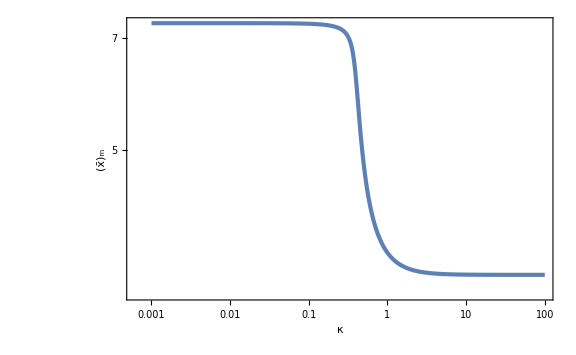

```mathematica
Figxm=ListLogLogPlot[xmList,FrameLabel->{κ,Subscript[OverBar[x], "m"]}]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa,alphas];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==267/1000,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

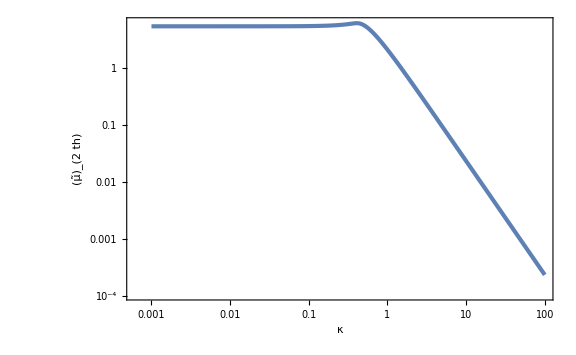

```mathematica
Figmuth=ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]}]
```

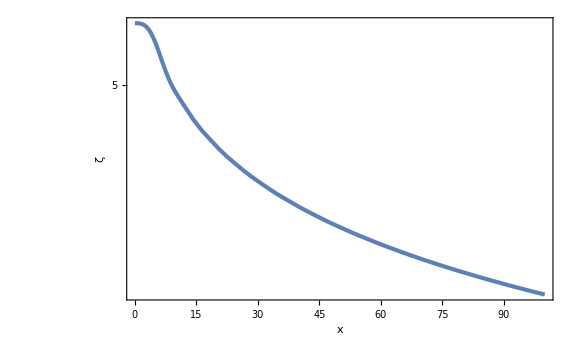

```mathematica
LogPlot[zetax[x,muthint[k],k,alphas]/.{k->0.1},{x,0.01,100},PlotRange->Full,FrameLabel->{x,ζ}]
```

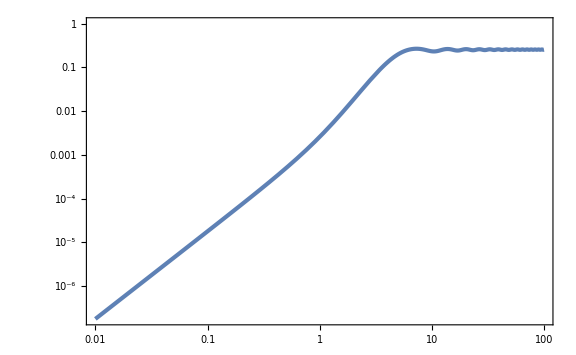

```mathematica
LogLogPlot[CompactC[x,muthint[k],k,alphas]/.{k->10^-1},{x,0.01,100}(*,WorkingPrecision->50,FrameLabel->{x,𝒞}*)]
```

```mathematica
muthint[10]
```

0.0232389954693570941588428796520054860680958007515

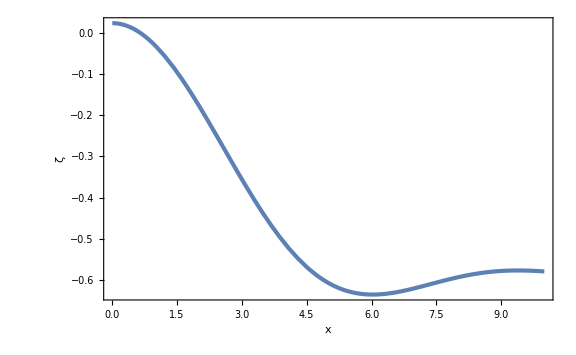

```mathematica
Plot[zetax[x,muthint[k],k,alphas]/.{k->10},{x,0,10},WorkingPrecision->50,FrameLabel->{x,ζ}]
```

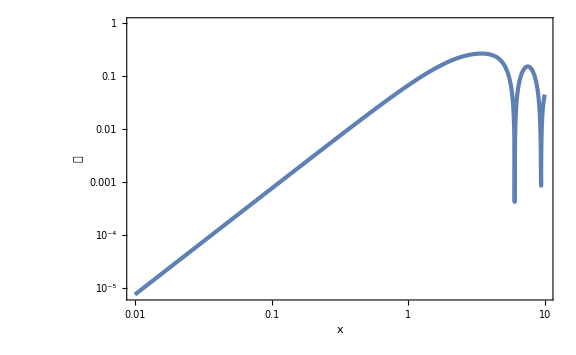

```mathematica
LogLogPlot[Abs[CompactC[x,muthint[k],k,alphas]/.{k->10}],{x,0.01,10},WorkingPrecision->50,FrameLabel->{x,𝒞}]
```

## monochromatic 256 16

```mathematica
npeak=16;
nbias=16;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
kbias=2π nbias/NL
```

π/8

π/8

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.0242276

0.0237815

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
FigLap3D=ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

```mathematica
Export["mono_lap_3D.pdf",FigLap3D];
```

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
(*peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]*)
peak2D=Flatten[Map[{If[#[[2]]>NL/2,ny=#[[2]]-NL,ny=#[[2]]];If[#[[3]]>NL/2,nz=#[[3]]-NL,nz=#[[3]]];
{ny,nz,#[[4]]}}&,Select[peakdata,#[[1]]==255&]],1]
```

{{53,110,0.265677},{95,-16,0.120924},{104,-71,0.232657},{-124,-113,0.489872},{-111,58,0.266629},{-109,4,0.183461},{-93,72,0.365621},{-90,-122,0.292102},{-89,-121,0.316246},{-82,23,0.27632},{-71,-70,0.303311},{-42,58,0.334987},{-35,39,0.433309},{-25,78,0.290148},{-17,74,0.177023},{-11,50,0.222175},{-9,1,0.352842},{-2,-95,0.258579}}

```mathematica
(*map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];*)
map2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,mapdata[[NL^2 255+NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,dW},ColorFunction->ColorData["Gradients"][[37]],Mesh->None,PlotRange->{-0.5,1.5},ViewPoint->Front]
```

```mathematica
FigLap2D=Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

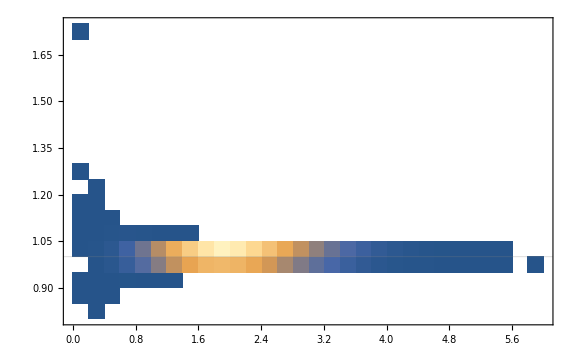

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

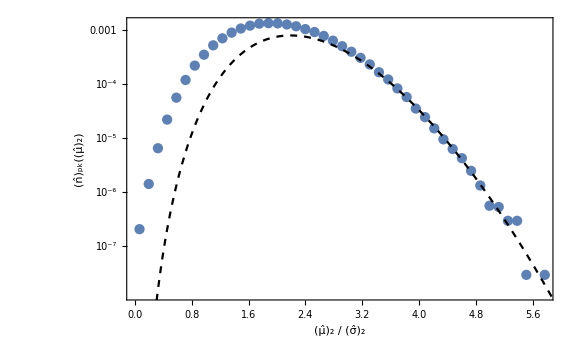

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[7]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[7]]]]}&,mukdata];
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

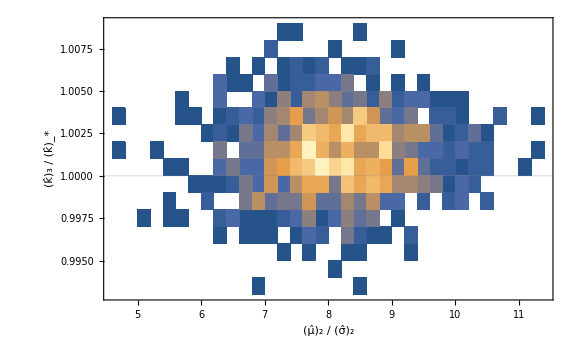

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

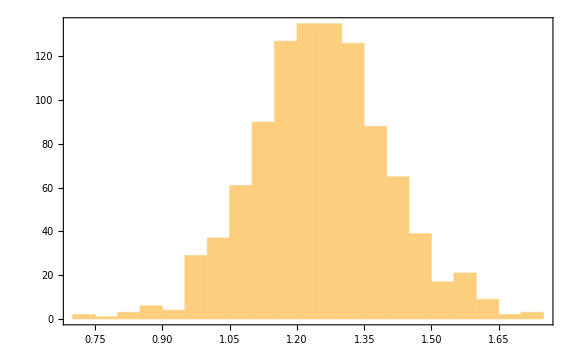

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/20

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

7/10

7/4

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

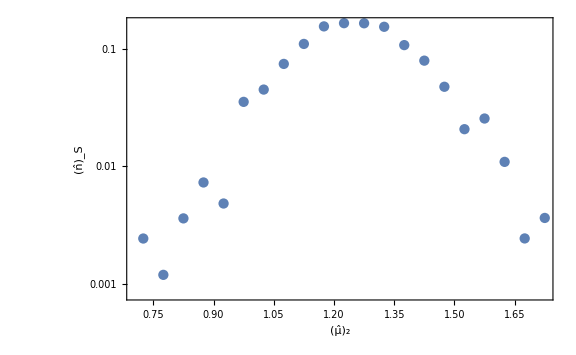

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,7]]]+Variance[mu2binning[mu2][[All,7]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,7]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,7]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,7]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,7]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

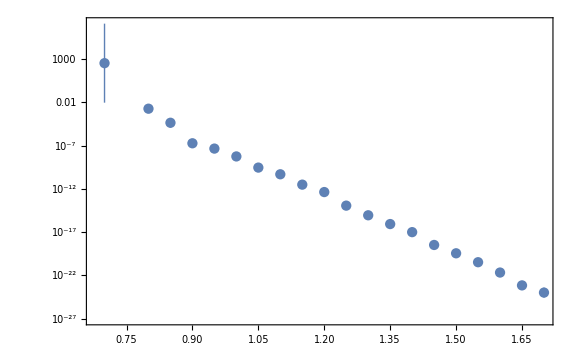

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

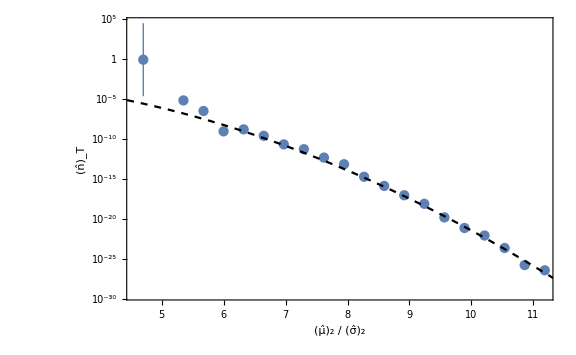

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,4,15},PlotStyle->{Black,Dashed}]]
```

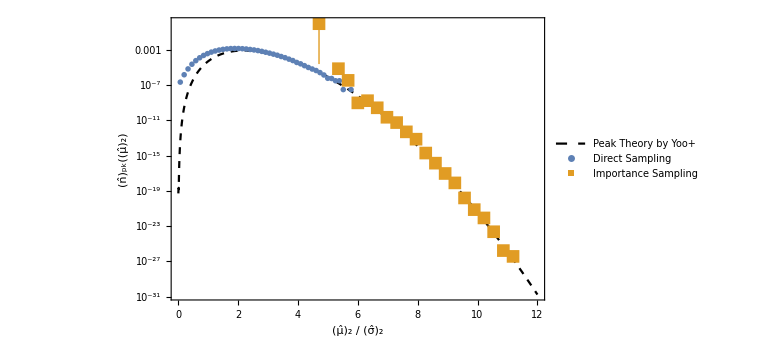

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,12},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],(*Row[{Subscript[N, L]==ToString[NL],", ",n_*==ToString[npeak]}]*)None}},PlotLegends->Placed[LineLegend[{"Peak Theory by Yoo+"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.3}]],
ListLogPlot[nmu2Lat,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.2}]],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.3,0.1}]]]
```

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"}]
```

-Graphics-

```mathematica
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36,Cth->0.533};
```

```mathematica
MPBHList=Map[{#[[3]],MPBH[#[[4]],#[[5]],#[[6]]],#[[7]]}&,Select[mukdata,#[[6]]>0.533&]];
```

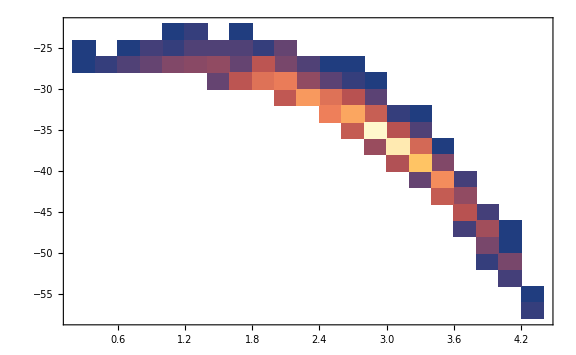

```mathematica
DensityHistogram[MPBHList[[All,2;;3]]]
```

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
```

1/10

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last
```

-8/5

3/2

```mathematica
lnMbinning[lnM_]:=Select[MPBHList,lnM<=Log[#[[2]]]<lnM+DlnM&];
k33sumlnM[lnM_]:=Total[(lnMbinning[lnM][[All,1]])^3]
```

```mathematica
nSlnMList=Table[{lnM+DlnM/2,k33sumlnM[lnM]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];
```

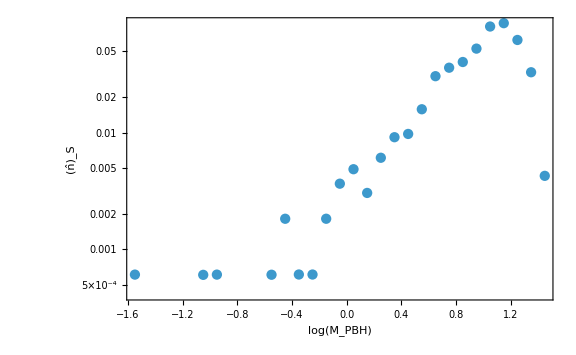

```mathematica
ListLogPlot[nSlnMList,Joined->False,FrameLabel->{Log[Subscript[M, PBH]],Subscript[OverHat[n], "S"]}]
```

```mathematica
wlnMList=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Exp[Mean[lnMbinning[lnM][[All,3]]]+Variance[lnMbinning[lnM][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrp=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrm=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
```

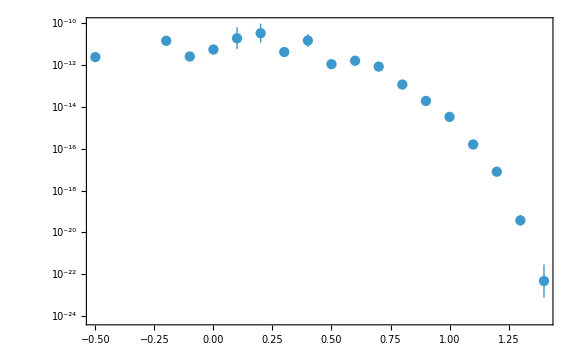

```mathematica
ListLogPlot[Table[{wlnMList[[i,1]],wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[wlnMList]}],Joined->False]
```

```mathematica
nTlnMList=Table[{nSlnMList[[i,1]]//Exp,nSlnMList[[i,2]]wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[nSlnMList]}];
```

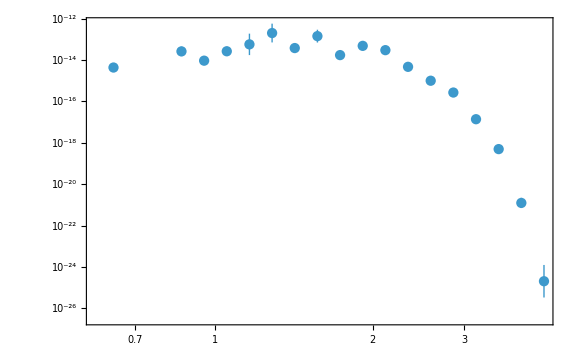

```mathematica
ListLogLogPlot[nTlnMList,Joined->False]
```

```mathematica
xc Sinc'[xc]/.{xc->2.74}
```

-1.0631

```mathematica
Cm[mu2_]=2/3(1-(1+xc Sinc'[xc] σ1^2/σ2^2 mu2)^2)/.{xc->2.74};
```

```mathematica
dlnMdmu2[mu2_]=2 σ1^2/σ2^2 Sinc[xc]+γ/(Cm[mu2]-Cth)Cm'[mu2]/.{Cth->0.533,γ->0.36,xc->2.74};
```

```mathematica
nPBHpk[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/(σ2 Sqrt[As])] 1/Sqrt[2π σ2^2 As] Exp[-mu2^2/(2 σ2^2 As)] dlnMdmu2[mu2]^-1/.{As->5 10^-3};
```

```mathematica
Mpeak[mu2_]=xc^2 Exp[2 σ1^2/σ2^2 Sinc[xc]mu2](Cm[mu2]-Cth)^γ/.{Cth->0.533,γ->0.36,xc->2.74};
```

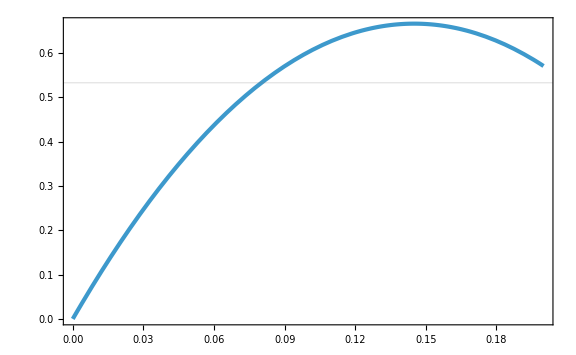

```mathematica
Plot[Cm[mu2],{mu2,0,0.2},GridLines->{None,{0.533}}]
```

```mathematica
mu2th=mu2/.FindRoot[Cm[mu2]==0.533,{mu2,0.1}]
```

0.0801059

```mathematica
nPBHpkList=Table[{Mpeak[mu2th+10^dlnmu2],nPBHpk[mu2th+10^dlnmu2]},{dlnmu2,-5,-1,10^-2}];
```

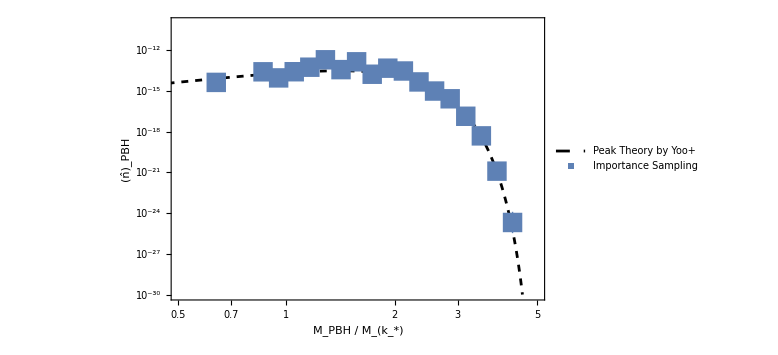

```mathematica
Show[ListLogLogPlot[nPBHpkList,PlotStyle->{Black,Dashed},PlotRange->{{0.5,5},{10^-30,10^-10}},FrameLabel->{"M_PBH / M_(k_*)",Subscript[OverHat[n], PBH]},PlotLegends->Placed[{"Peak Theory by Yoo+"}(*LineLegend[{"Peak Theory by Yoo+"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]]*),{0.4,0.26}]],ListLogLogPlot[nTlnMList,Joined->False,PlotMarkers->Style["■",Color[1],20],IntervalMarkersStyle->{Color[1],Thick},PlotLegends->Placed[{"Importance Sampling"}(*PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]]*),{0.4,0.14}]]]
```

### wrong bias

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>".csv"];
Ntot=Length[mukdata]
```

100

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

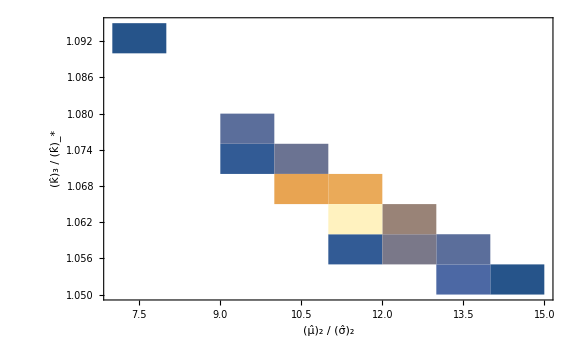

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

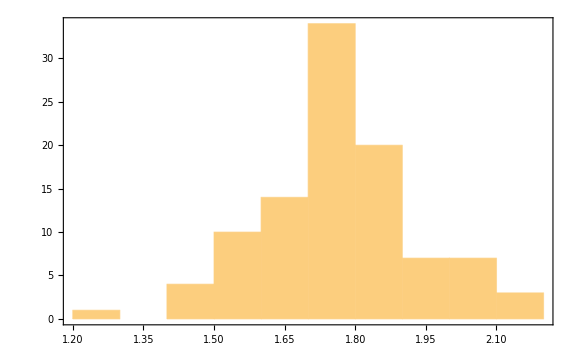

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/10

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

6/5

11/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)(*(Length[mu2binning[mu2]] kbias^3)/(Ntot Dmu2)*)},{mu2,mu2min,mu2max,Dmu2}];
```

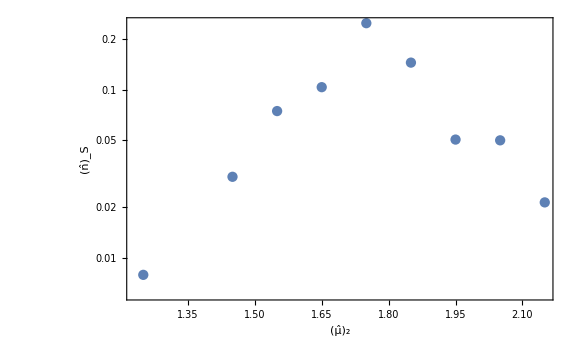

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

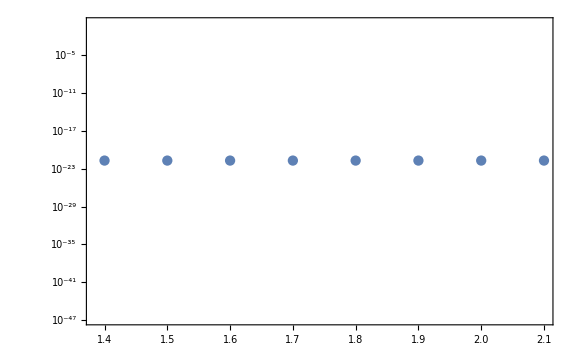

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

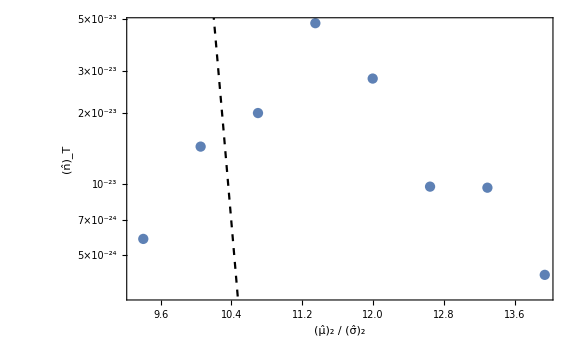

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

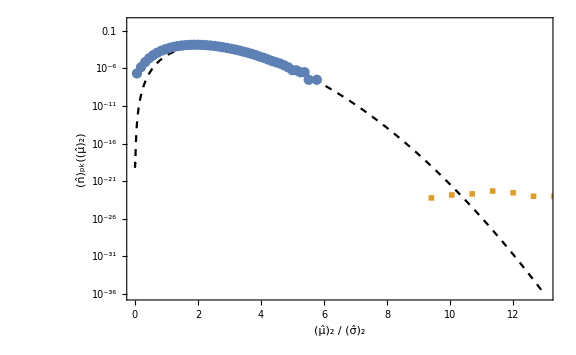

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

### test

```mathematica
seed=3;
```

```mathematica
mapdata=Import["data/mono_map_"<>ToString[seed]<>".csv"][[1]];
```

```mathematica
Variance[mapdata]
```

0.985825

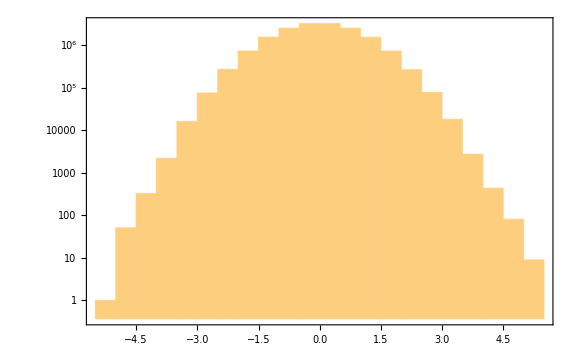

```mathematica
Histogram[mapdata,ScalingFunctions->"Log",PlotRange->Full]
```

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->g[x,y,z]]]
```

-Graphics3D-

```mathematica
shiftedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,mapdata[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
powerdata=Import["data/mono_power_0.dat"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

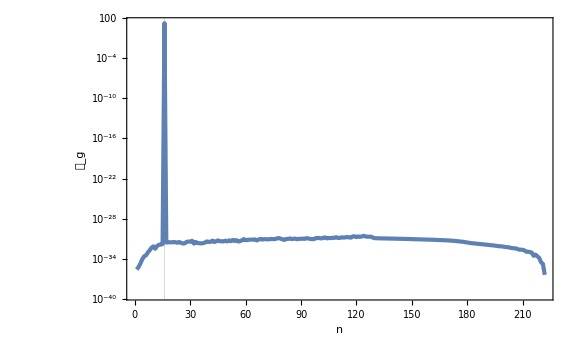

```mathematica
ListLogPlot[powerList,GridLines->{{npeak},None},FrameLabel->{n,Subscript[𝒫, g]}]
```

```mathematica
powerList[[17]]
```

{16,16.2188}

```mathematica
biasedmap=Import["data/mono_biased_0.dat"][[1]];
lapmap=Import["data/mono_laplacian_0.dat"][[1]];
```

```mathematica
shiftedbias2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedbias2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,biasedmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedmap2D,PlotRange->Full,AxesLabel->{y,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
lapmap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[lapmap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedlap2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,lapmap[[NL nyt+nzt+1]]},{ny,-2npeak,2npeak},{nz,-2npeak,2npeak}],1];
```

```mathematica
ListPlot3D[focusedlap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

### bias

```mathematica
mapdata=Import["data/mono_bias_laplacian_256_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.0249808

0.0237815

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

```mathematica
peakdata=Import["data/mono_bias_peak_256_0.csv"];
```

```mathematica
Select[peakdata,#[[4]]/σ2>10&]
```

{{255,255,1,1.62863,0.391846}}

```mathematica
peak2D=Flatten[Map[{If[#[[2]]>NL/2,ny=#[[2]]-NL,ny=#[[2]]];If[#[[3]]>NL/2,nz=#[[3]]-NL,nz=#[[3]]];
{ny,nz,#[[4]]}}&,Select[peakdata,#[[1]]==255&]],1]
```

{{46,-72,0.24552},{61,-34,0.274946},{75,-67,0.264587},{105,-71,0.241079},{-124,-113,0.478127},{-115,46,0.359853},{-109,4,0.17108},{-106,60,0.300908},{-94,71,0.336816},{-89,-121,0.339492},{-88,-120,0.34782},{-71,-70,0.327307},{-46,116,0.329681},{-42,57,0.318848},{-35,38,0.467295},{-31,24,0.253736},{-25,78,0.299853},{-11,50,0.281742},{-8,87,0.382089},{-1,1,1.62863}}

```mathematica
map2D=Flatten[Table[If[ny<0,nyt=ny+NL,nyt=ny];
If[nz<0,nzt=nz+NL,nzt=nz];
{ny,nz,mapdata[[NL^2 255+NL nyt+nzt+1]]},{ny,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,Subscript[dW, "b"]},ColorFunction->ColorData["Gradients"][[37]],Mesh->None,PlotRange->{-0.5,1.5},ViewPoint->Front]
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g_(<b>)"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None](*,
ListPointPlot3D[peak2D,PlotStyle->Black]*)]
```

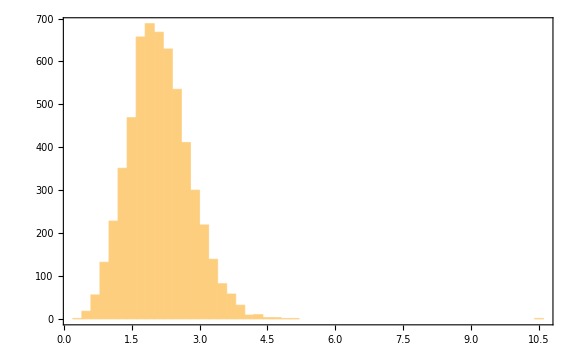

```mathematica
Histogram[peakdata[[All,4]]/σ2,PlotRange->Full]
```

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_256_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

-Graphics-

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[N, L]==256}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

-Graphics-

## monochromatic 256 8

```mathematica
npeak=8;
NL=256;
```

```mathematica
kpeak=2π npeak/NL
```

π/16

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.00162418

0.00148634

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{13,102,0.0435504},{119,133,0.0580749},{167,72,0.067136},{206,75,0.0668344}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

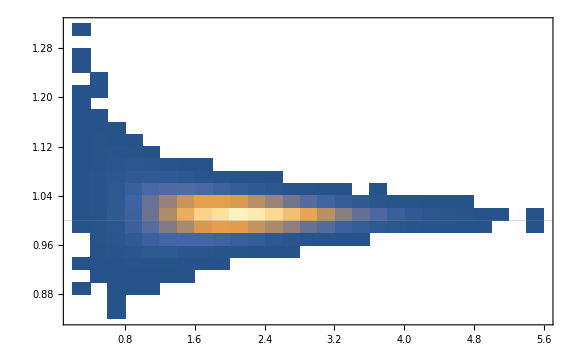

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

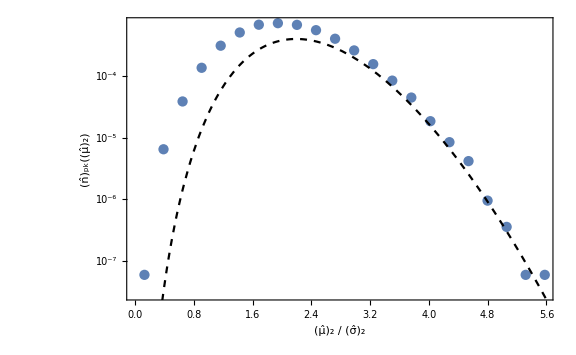

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

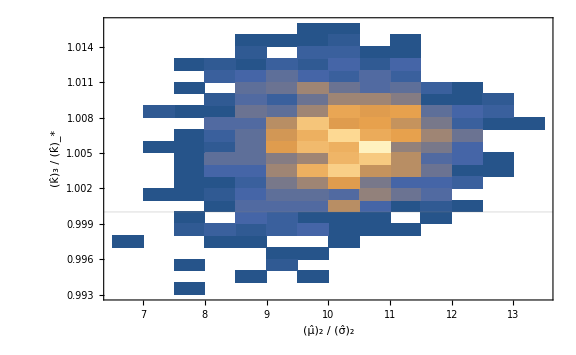

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

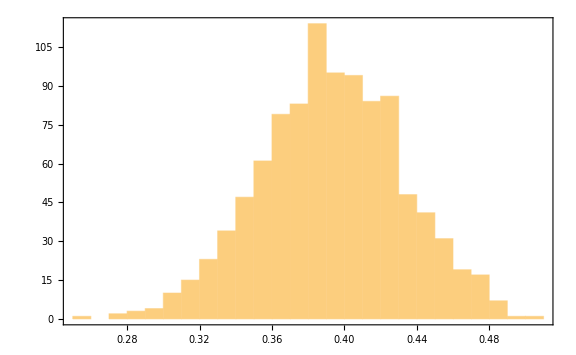

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/100

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

1/4

51/100

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

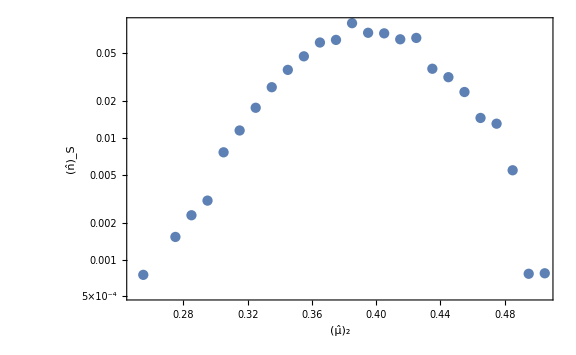

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

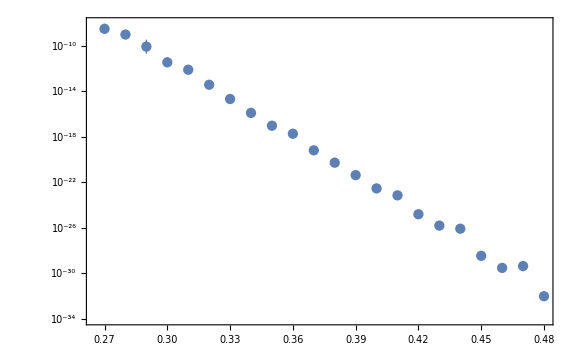

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

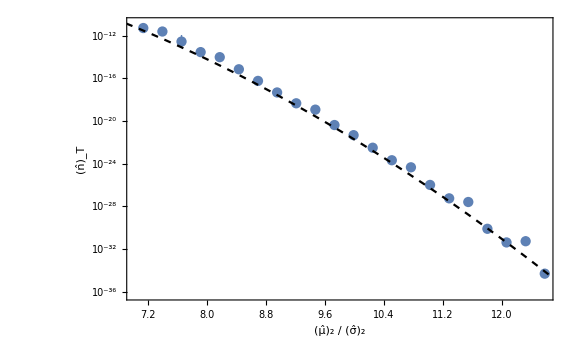

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

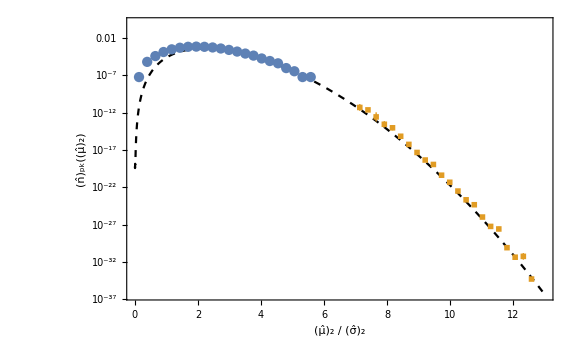

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## monochromatic 128 16

```mathematica
npeak=2^4;
NL=128;
```

```mathematica
kpeak=2π npeak/NL
```

π/4

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.387642

0.380504

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{6,73,1.07112},{17,119,0.970761},{27,56,1.10484},{32,112,1.01206},{35,87,1.04952},{39,96,1.05852},{44,86,0.529736},{49,14,0.74006},{49,121,0.30645},{53,93,0.826954},{57,77,0.652277},{60,49,1.59837},{67,72,1.84326},{73,30,0.900259},{75,75,1.14675},{83,76,1.45891},{88,46,1.26667},{91,38,0.406844},{105,127,2.03643},{111,74,1.29881},{117,40,1.14442},{120,7,1.14484},{120,39,0.57786},{121,38,0.537725},{123,26,0.843453},{125,45,1.49959},{125,96,0.95891}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

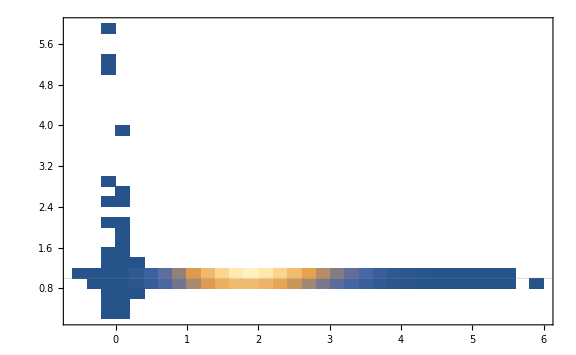

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

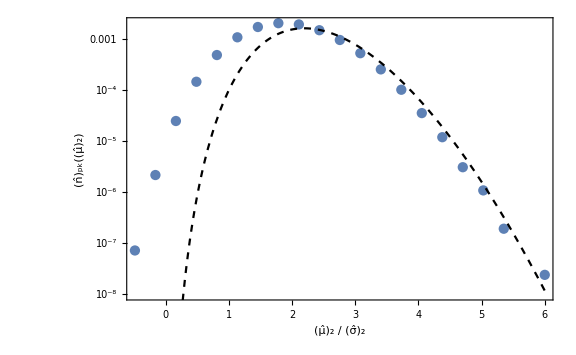

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

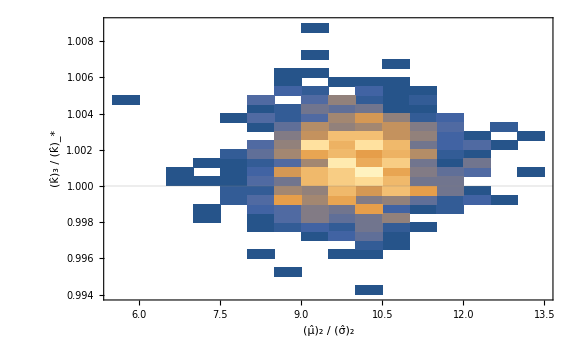

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

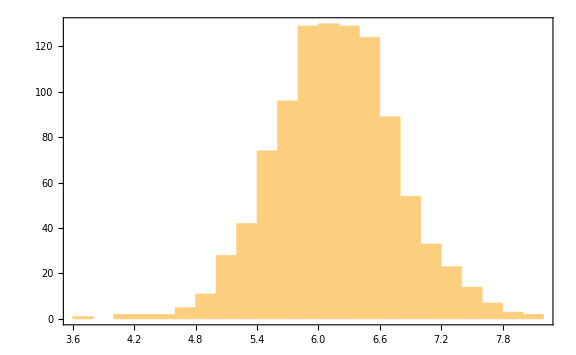

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/5

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

18/5

41/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

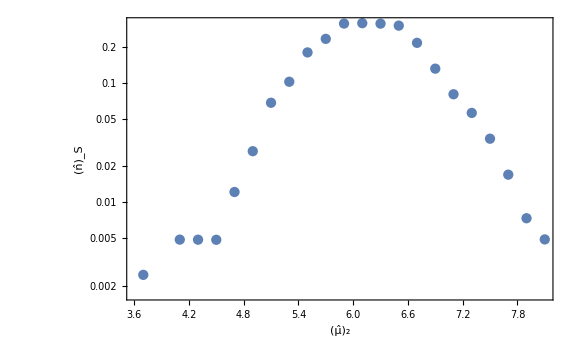

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

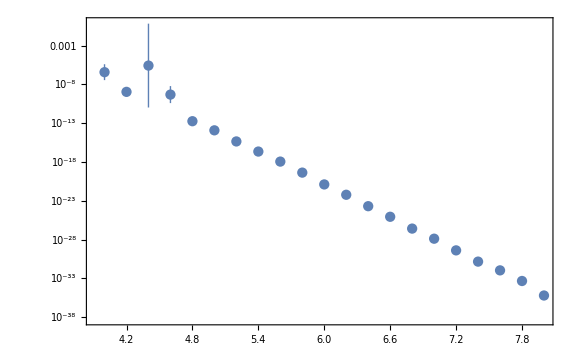

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

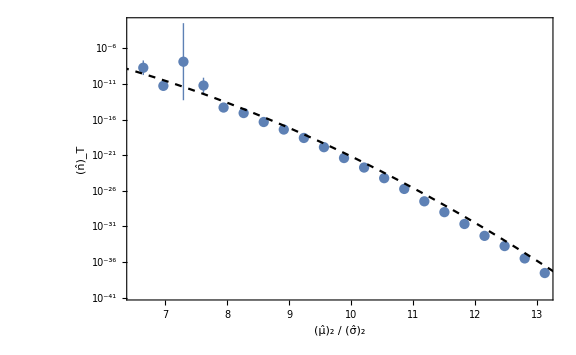

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

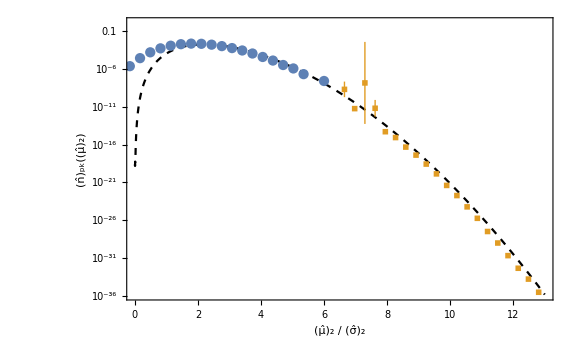

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## monochromatic 128 8

```mathematica
npeak=2^3;
NL=128;
```

```mathematica
kpeak=2π npeak/NL
```

π/8

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.0259868

0.0237815

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{23,114,0.349079},{38,80,0.412598},{51,49,0.517785},{103,38,0.262935},{1,8,0.491576}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

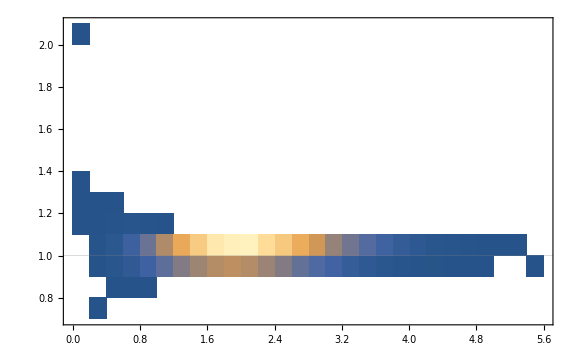

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

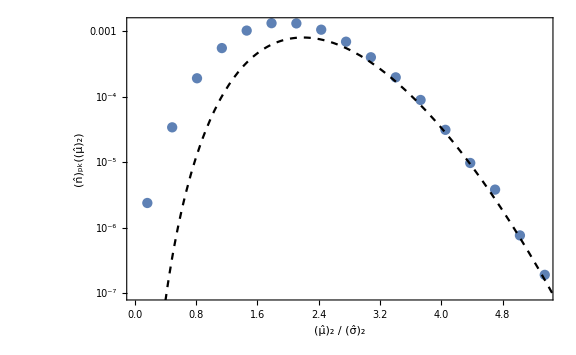

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

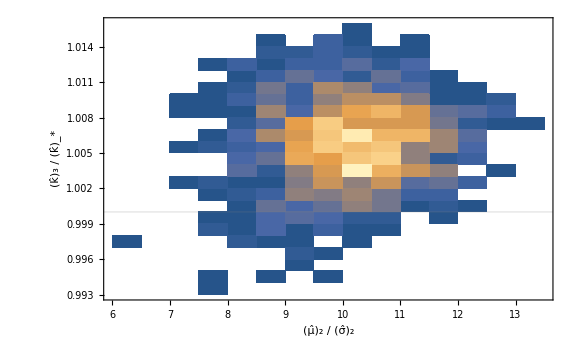

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

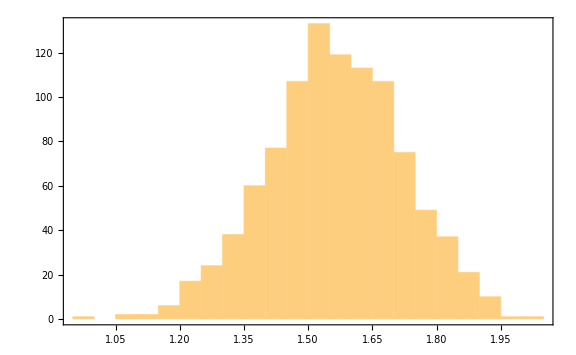

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/20

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

19/20

41/20

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

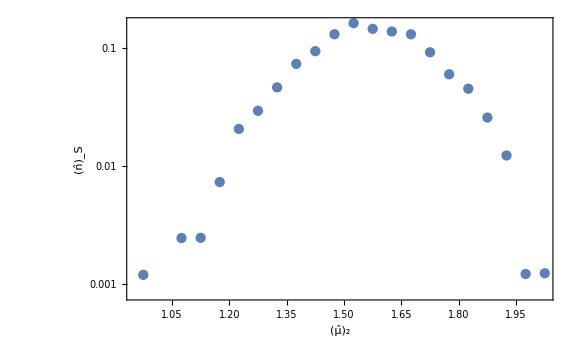

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

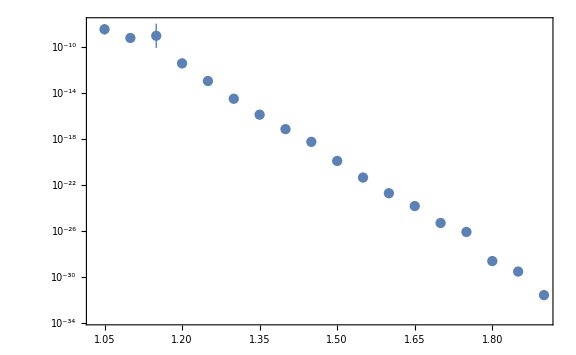

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

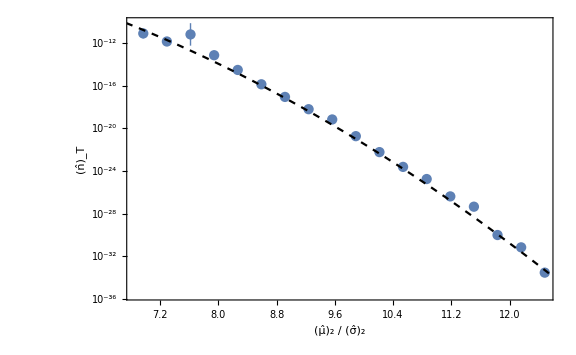

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

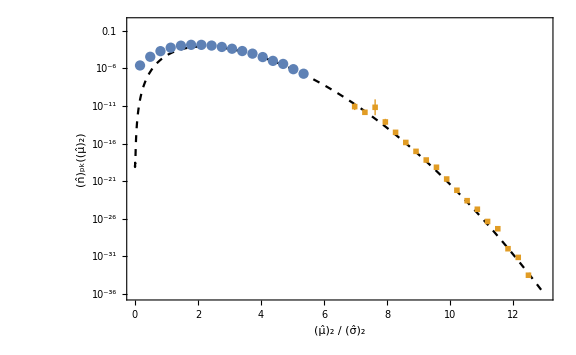

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## monochromatic 64 8

```mathematica
npeak=2^3;
NL=64;
```

```mathematica
kpeak=2π npeak/NL
```

π/4

```mathematica
σ1=kpeak;
σ2=kpeak^2;
σ3=kpeak^3;
σ4=kpeak^4;
```

### peak

```mathematica
mapdata=Import["data/mono_laplacian_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"][[1]];
```

```mathematica
Variance[mapdata]
kpeak^4//N
```

0.415791

0.380504

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]]
```

{{8,17,1.94219},{12,57,1.41307},{20,41,1.56269},{26,25,2.07114},{52,20,1.01936},{52,61,1.8886},{54,53,0.939033},{1,4,1.92405}}

```mathematica
map2D=Flatten[Table[{ny,nz,mapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[map2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=100;
mukList=Flatten[Table[Import["data/mono_peak_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

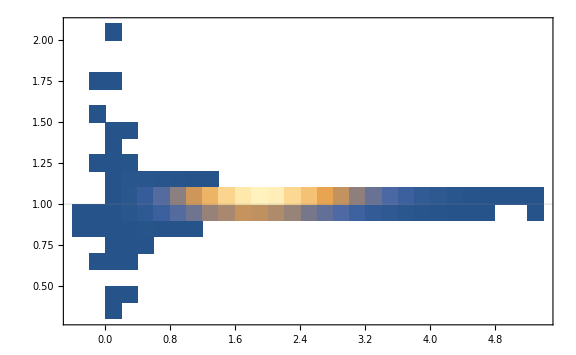

```mathematica
DensityHistogram[mukList.DiagonalMatrix[{1/σ2,1/kpeak}],GridLines->{None,{1}}]
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

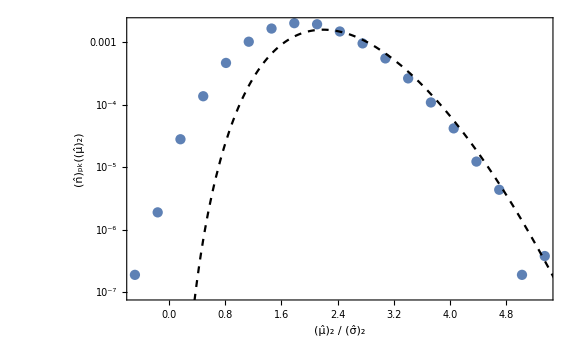

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,6},PlotStyle->{Dashed,Black}]]
```

### importance sampling

```mathematica
mukdata=Import["data/mono_muk_"<>ToString[NL]<>"_"<>ToString[npeak]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kpeak,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

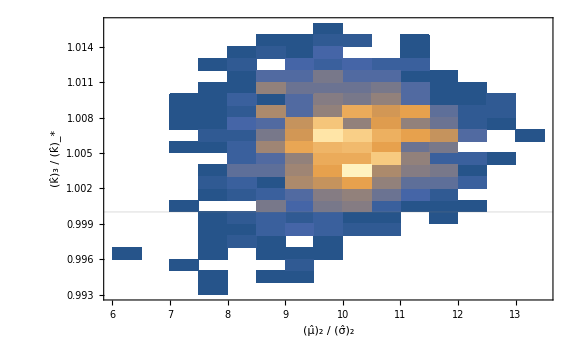

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kpeak}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",SubStar[OverHat[k]]}]},GridLines->{None,{1}}]
```

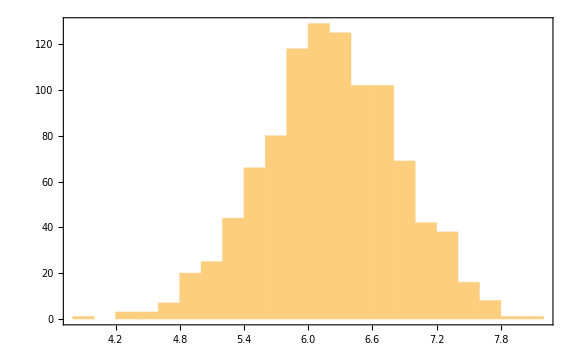

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/5

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

19/5

41/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

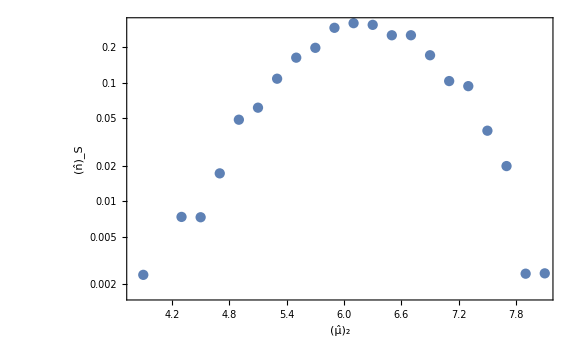

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

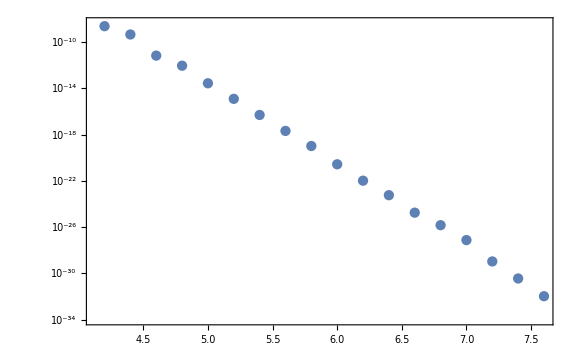

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
nmu2PT[mu2_]=kpeak^3/(6π)^(3/2) f[mu2/σ2] 1/Sqrt[2π σ2^2] Exp[-mu2^2/(2 σ2^2)];
```

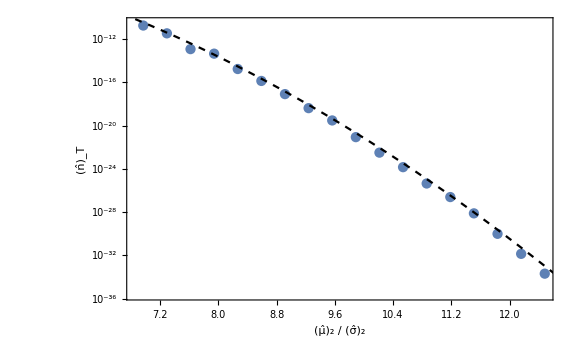

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

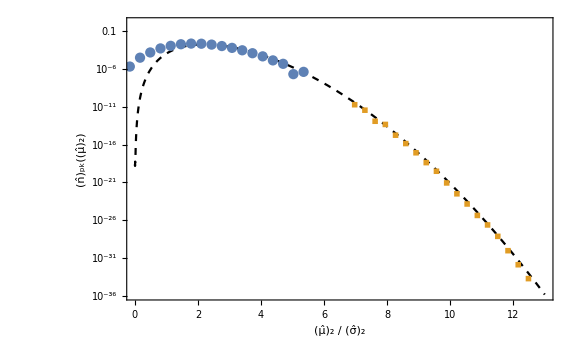

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

## log normal

```mathematica
calPg[lnk_]=1/Sqrt[2π s2] Exp[(-(lnk-lnks)^2)/(2s2)];
```

```mathematica
σn2[n_]=E^(2 n^2 s2)ks^(2n);
```

```mathematica
Simplify[Sqrt[3 σn2[n]/σn2[n+1]],{s2>0,n>0,ks>0}]
```

(√3 ⅇ^(-((1+2 n) s2)))/ks

```mathematica
Simplify[Integrate[Exp[2n lnk]calPg[lnk],{lnk,-∞,∞}]/σn2[n]/.{lnks->Log[ks]},{s2>0,ks>0,n>0}]
```

1

```mathematica
γn=Simplify[σn2[n]/Sqrt[σn2[n-1]σn2[n+1]],{ks>0,n>0,s2>0}]
```

ⅇ^(-2 s2)

```mathematica
Normal[Series[1-γn^2,{s2,0,1}]]
```

4 s2

```mathematica
Normal[Series[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2)),{s2,0,0}]]
```

-(-ν+ξ)^2/(8 s2)+1/4 (-ν^2-ξ^2)

```mathematica
Normal[Series[(1/(2π Sqrt[1-γn^2])Exp[-1/2(ν^2+(ξ-γn ν)^2/(1-γn^2))])/(1/Sqrt[2π] Exp[-ν^2/2] 1/Sqrt[2π 4s2] Exp[-1/2(ξ-ν)^2/(4s2)]),{s2,0,0}]]
```

ⅇ^(1/4 (ν^2-ξ^2))

```mathematica
Sqrt[50 2/(Floor[Sqrt[3]NL]-1)]//N
```

0.475651

```mathematica
1/2 0.48^2(Floor[Sqrt[3]NL]-1)
```

50.9184

### s2 = 0.01

```mathematica
s2=0.01;
```

#### peak

```mathematica
mapdata=Import["data/LN0,01_map_0.csv"][[1]];
```

Import::nffil: File data/LN0,01_map_0.csv not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

```mathematica
Length[mapdata]
```

16777216

```mathematica
Variance[mapdata]
```

1.00468

```mathematica
lapdata=Import["data/LN0,1_laplacian_0.csv"][[1]];
```

```mathematica
dn=2^2;
lap3D=Flatten[Table[{nx,ny,nz,lapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[lap3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/LN0,1_peak_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]];
```

```mathematica
lap2D=Flatten[Table[{ny,nz,lapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[lap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=10;
mukList=Flatten[Table[Import["data/LN0,01_peak_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

Import::nffil: File data/LN0,01_peak_0.csv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Import::nffil: File data/LN0,01_peak_1.csv not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Import::nffil: File data/LN0,01_peak_2.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

```mathematica
Length[mukList]
```

322160

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
σ2^2
```

0.0529267

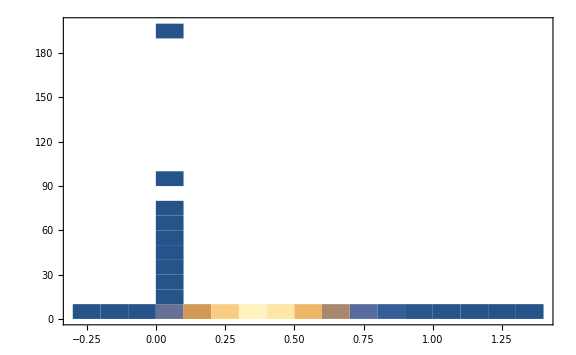

```mathematica
DensityHistogram[mukList,GridLines->{None,{kpeak}}]
```

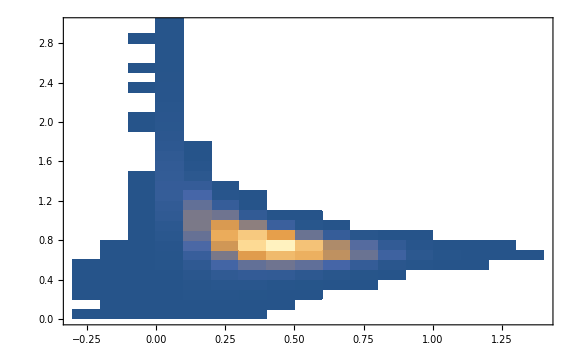

```mathematica
DensityHistogram[mukList,{Automatic,{0.1}},GridLines->{None,{kpeak}},PlotRange->{Full,{0,3}}]
```

```mathematica
HistogramList[mukList[[All,1]]]
```

{{-2/5,-3/10,-1/5,-1/10,0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5},{6,78,630,3519,12833,31659,55547,69578,64982,45008,24036,9989,3302,780,166,37,7,3}}

```mathematica
Dnu2=HistogramList[mukList[[All,1]]/σ2][[1,2]]-HistogramList[mukList[[All,1]]/σ2][[1,1]];
nu2min=Mean[HistogramList[mukList[[All,1]]/σ2][[1,1;;2]]];
nnu2Lat=Table[{nu2min+Dnu2(i-1),(HistogramList[mukList[[All,1]]/σ2][[2,i]])/(Dnu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]/σ2][[2]]]}];
```

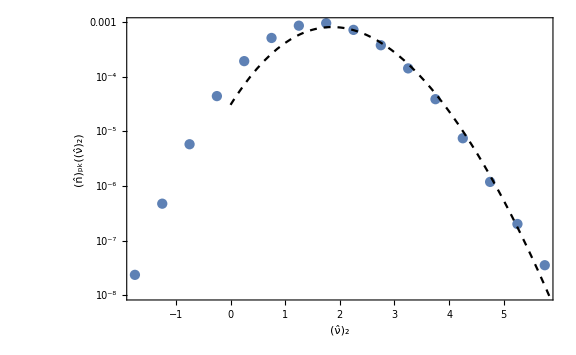

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]],None},{Subscript[OverHat[ν], 2],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black}]]
```

```mathematica
HistoList=HistogramList[mukList,{{1/10},{1/10^2}}];
```

```mathematica
HistoList
```

```mathematica
Dmu2=HistoList[[1,1,2]]-HistoList[[1,1,1]]
Dk3=HistoList[[1,2,2]]-HistoList[[1,2,1]]
mu2min=Mean[HistoList[[1,1,1;;2]]];
k3min=Mean[HistoList[[1,2,1;;2]]];
npkLat=Table[{mu2min+Dmu2(i-1),k3min+Dk3(j-1),Log10[HistoList[[2,i,j]]/(Dmu2 Dk3 Nsim NL^3)]},{i,Length[HistoList[[2]]]},{j,Length[HistoList[[2,1]]]}];
```

1/10

1/100

```mathematica
k3min
```

3/200

```mathematica
Show[ListDensityPlot[Flatten[npkLat,1],PlotLegends->Automatic,PlotRange->{{0,1},{0,4}},PlotRangePadding->None,GridLines->{None,{kpeak}}],
ContourPlot[Log10[npkPT[mu2,k3]],{mu2,0,2},{k3,0,5},ContourShading->None,Contours->{-1,-2,-3,-4},PlotRange->Full]]
```

-Graphics-

```mathematica
k50=npkLat[[All,50,All]][[1,2]];
k55=npkLat[[All,55,All]][[1,2]];
k60=npkLat[[All,60,All]][[1,2]];
k65=npkLat[[All,65,All]][[1,2]];
k70=npkLat[[All,70,All]][[1,2]];
k100=npkLat[[All,100,All]][[1,2]];
```

```mathematica
k50//N
k55//N
k60//N
k65//N
k70//N
k100//N
```

0.505

0.555

0.605

0.655

0.705

1.005

```mathematica
npkLat50=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,50,All]],#[[3]]>-100&]];npkLat55=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,55,All]],#[[3]]>-100&]];npkLat60=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,60,All]],#[[3]]>-100&]];npkLat65=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,65,All]],#[[3]]>-100&]];npkLat70=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,70,All]],#[[3]]>-100&]];
npkLat100=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,100,All]],#[[3]]>-100&]];
```

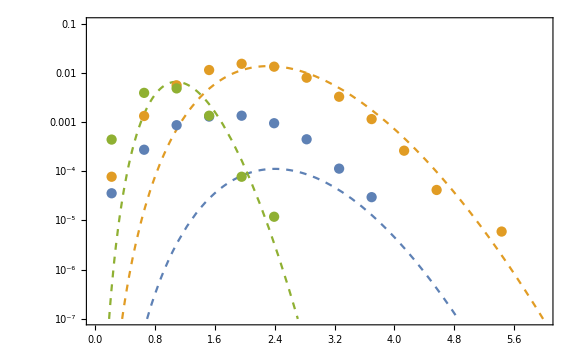

```mathematica
Show[LogPlot[{npkPT[mu2 σ2,k50],npkPT[mu2 σ2,k70],npkPT[mu2 σ2,k100]},{mu2,0,6},PlotStyle->Dashed,PlotRange->{10^-7,10^-1}],
ListLogPlot[{npkLat50,npkLat70,npkLat100},Joined->False]]
```

#### importance sampling GB

```mathematica
Sqrt[50 4Sqrt[π]]//N
```

18.8279

```mathematica
npeak=16;
nbias=16;
NL=256;
kpeak=(2π npeak)/NL
```

π/8

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
kbias=2π nbias/NL
```

π/8

```mathematica
mukdata=Import["data/LN_muk_0,01_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_GB.csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[7]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[7]]]]}&,mukdata];
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Subscript[OverHat[ν], 2],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{Sqrt[σ2/σ4],1}],ChartLegends->Automatic,FrameLabel->{Subscript[OverTilde[k], 3],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

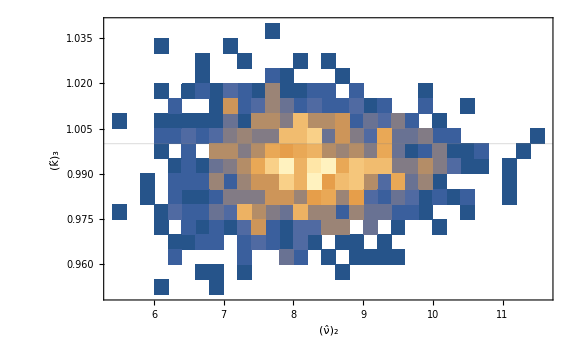

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,Sqrt[σ2/σ4]}],FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverTilde[k], 3]},GridLines->{None,{1}}]
```

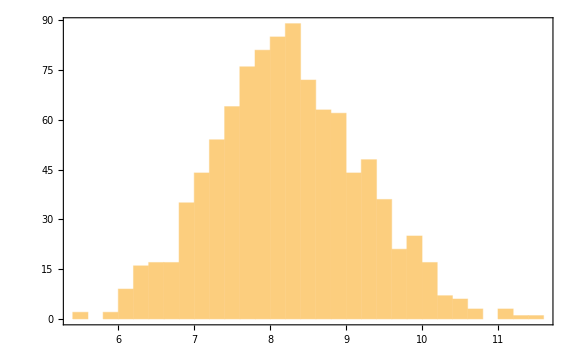

```mathematica
Histogram[mukdata[[All,2]]/σ2]
```

```mathematica
Dnu2=HistogramList[mukdata[[All,2]]/σ2][[1,2]]-HistogramList[mukdata[[All,2]]/σ2][[1,1]]
```

1/5

```mathematica
nu2min=HistogramList[mukdata[[All,2]]/σ2][[1,1]]
nu2max=HistogramList[mukdata[[All,2]]/σ2][[1]]//Last
```

27/5

58/5

```mathematica
nu2binning[nu2_]:=Select[mukdata,nu2(*-Dmu2/2*)<=(#[[2]])/σ2<nu2+(*Dmu2/2*)Dnu2&];
k33sum[nu2_]:=Total[(nu2binning[nu2][[All,3]])^3]
```

```mathematica
nSnu2List=Table[{nu2+Dnu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[nu2]/(Ntot Dnu2)},{nu2,nu2min,nu2max,Dnu2}];
```

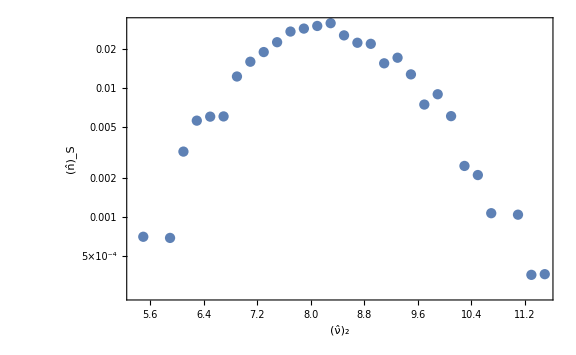

```mathematica
ListLogPlot[nSnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wnu2List=Table[{nu2,If[Length[nu2binning[nu2]]>1,Exp[Mean[nu2binning[nu2][[All,7]]]+Variance[nu2binning[nu2][[All,7]]]/2],0]},{nu2,nu2min,nu2max,Dnu2}];
wnu2errp=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2min,nu2max,Dnu2}];
wnu2errm=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[-Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2min,nu2max,Dnu2}];
```

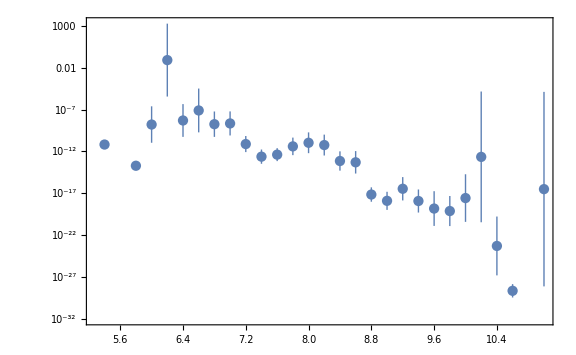

```mathematica
ListLogPlot[Table[{wnu2List[[i,1]],wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[wnu2List]}],Joined->False]
```

```mathematica
nTnu2List=Table[{nSnu2List[[i,1]],nSnu2List[[i,2]]wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[nSnu2List]}];
```

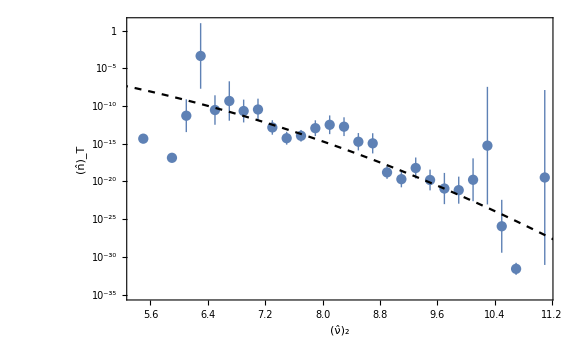

```mathematica
Show[ListLogPlot[nTnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "T"]}],LogPlot[nnu2PT[x],{x,5,15},PlotStyle->{Black,Dashed}]]
```

```mathematica
Show[LogPlot[nnu2PT[x],{x,0,11},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]],None},{Subscript[OverHat[ν], 2],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak],", ",σ^2==0.1}]}},PlotLegends->Placed[LineLegend[{"Peak Theory"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.2,0.2}]],
ListLogPlot[nnu2Lat,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.2,0.2}]],ListLogPlot[nTnu2List,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.2,0.2}]]]
```

$Aborted

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"}]
```

-Graphics-

```mathematica
Cth=0.533(*0.45*);
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36(*,Cth->0.533*)};
```

```mathematica
MPBHList=Map[{#[[3]],MPBH[(*kpeak/(#[[3]])*)#[[4]],#[[5]],#[[6]]],#[[7]]}&,Select[mukdata,#[[6]]>Cth&]];
```

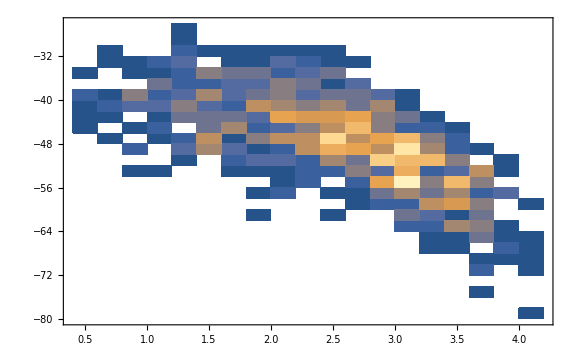

```mathematica
DensityHistogram[MPBHList[[All,2;;3]]]
```

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
```

1/5

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last
```

-1

8/5

```mathematica
lnMbinning[lnM_]:=Select[MPBHList,lnM<=Log[#[[2]]]<lnM+DlnM&];
k33sumlnM[lnM_]:=Total[(lnMbinning[lnM][[All,1]])^3]
```

```mathematica
nSlnMList=Table[{lnM+DlnM/2,k33sumlnM[lnM]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];
```

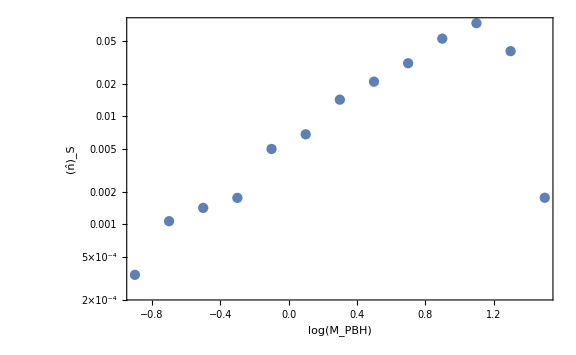

```mathematica
ListLogPlot[nSlnMList,Joined->False,FrameLabel->{Log[Subscript[M, PBH]],Subscript[OverHat[n], "S"]}]
```

```mathematica
wlnMList=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Exp[Mean[lnMbinning[lnM][[All,3]]]+Variance[lnMbinning[lnM][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrp=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrm=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
```

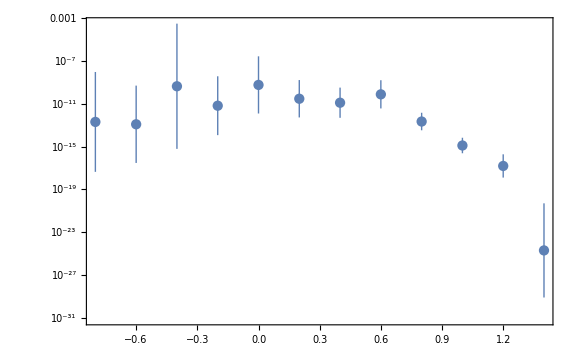

```mathematica
ListLogPlot[Table[{wlnMList[[i,1]],wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[wlnMList]}],Joined->False]
```

```mathematica
nTlnMList=Table[{nSlnMList[[i,1]]//Exp,nSlnMList[[i,2]]wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[nSlnMList]}];
```

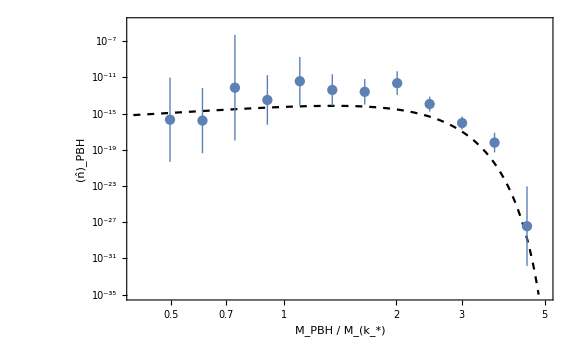

```mathematica
Show[ListLogLogPlot[Import["data/nPBH_LN_0,01_PT.csv"],PlotStyle->{Black,Dashed},PlotRange->{{0.4,5},{10^-35,10^-5}},FrameLabel->{"M_PBH / M_(k_*)",Subscript[OverHat[n], PBH]},PlotLegends->Placed[LineLegend[{"Peak Theory"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.3}]],
ListLogLogPlot[nTlnMList,Joined->False,PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.3,0.3}]]]
```

#### importance sampling monoB

```mathematica
nbias=16;
kbias=2π nbias/NL
```

π/8

```mathematica
mukdata=Import["data/LN_muk_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kbias,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",Subscript[OverHat[k], "B"]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

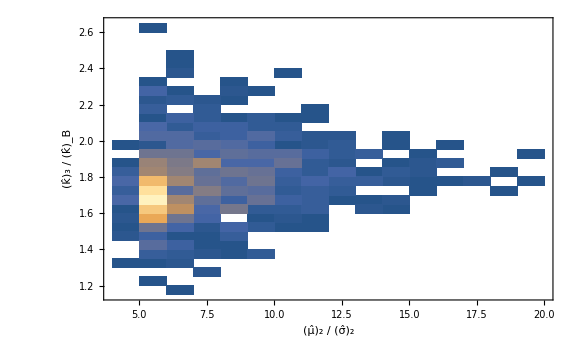

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kbias}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",Subscript[OverHat[k], "B"]}]},GridLines->{None,{1}}]
```

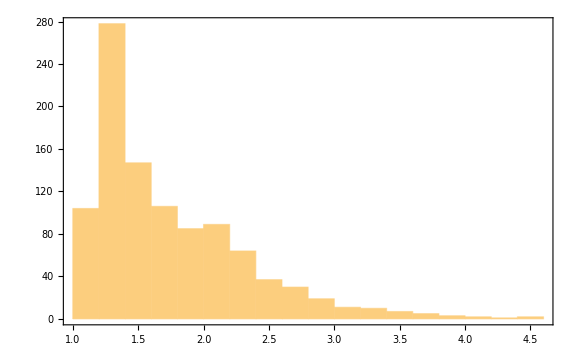

```mathematica
Histogram[mukdata[[All,2]]]
```

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/5

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

1

23/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

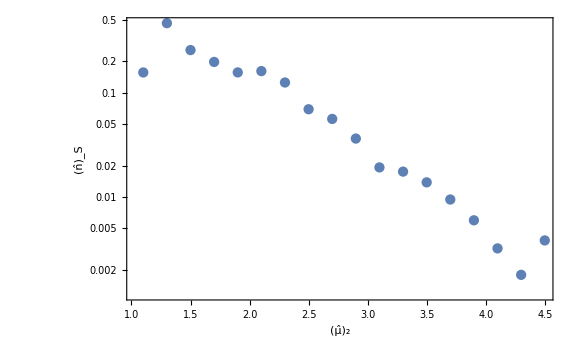

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

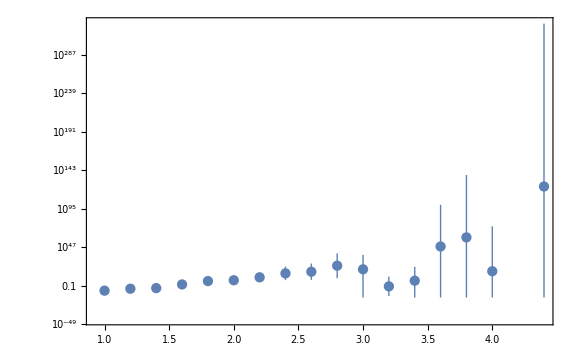

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

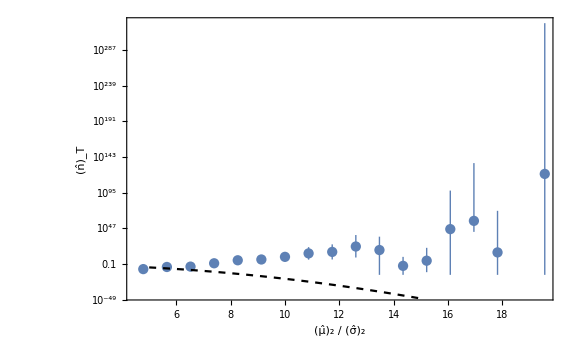

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

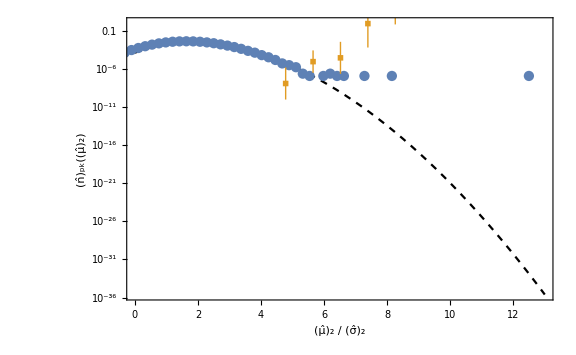

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

### s2 = 0.1

```mathematica
s2=0.1;
```

#### peak

```mathematica
mapdata=Import["data/LN0,1_map_0.csv"][[1]];
```

```mathematica
Length[mapdata]
```

16777216

```mathematica
Variance[mapdata]
```

1.00468

```mathematica
lapdata=Import["data/LN0,1_laplacian_0.csv"][[1]];
```

```mathematica
dn=2^2;
lap3D=Flatten[Table[{nx,ny,nz,lapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[lap3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/LN0,1_peak_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]];
```

```mathematica
lap2D=Flatten[Table[{ny,nz,lapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[lap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=10;
mukList=Flatten[Table[Import["data/LN0,1_peak_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

$Aborted

```mathematica
Length[mukList]
```

322160

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
σ2^2
```

0.0529267

```mathematica
DensityHistogram[mukList,GridLines->{None,{kpeak}}]
```

-Graphics-

```mathematica
DensityHistogram[mukList,{Automatic,{0.1}},GridLines->{None,{kpeak}},PlotRange->{Full,{0,3}}]
```

-Graphics-

```mathematica
HistogramList[mukList[[All,1]]]
```

{{-2/5,-3/10,-1/5,-1/10,0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5},{6,78,630,3519,12833,31659,55547,69578,64982,45008,24036,9989,3302,780,166,37,7,3}}

```mathematica
Dnu2=HistogramList[mukList[[All,1]]/σ2][[1,2]]-HistogramList[mukList[[All,1]]/σ2][[1,1]];
nu2min=Mean[HistogramList[mukList[[All,1]]/σ2][[1,1;;2]]];
nnu2Lat=Table[{nu2min+Dnu2(i-1),(HistogramList[mukList[[All,1]]/σ2][[2,i]])/(Dnu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]/σ2][[2]]]}];
```

```mathematica
Show[ListLogPlot[nnu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]],None},{Subscript[OverHat[ν], 2],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nnu2PT[nu2],{nu2,0,6},PlotStyle->{Dashed,Black}]]
```

-Graphics-

```mathematica
HistoList=HistogramList[mukList,{{1/10},{1/10^2}}];
```

```mathematica
HistoList
```

```mathematica
Dmu2=HistoList[[1,1,2]]-HistoList[[1,1,1]]
Dk3=HistoList[[1,2,2]]-HistoList[[1,2,1]]
mu2min=Mean[HistoList[[1,1,1;;2]]];
k3min=Mean[HistoList[[1,2,1;;2]]];
npkLat=Table[{mu2min+Dmu2(i-1),k3min+Dk3(j-1),Log10[HistoList[[2,i,j]]/(Dmu2 Dk3 Nsim NL^3)]},{i,Length[HistoList[[2]]]},{j,Length[HistoList[[2,1]]]}];
```

1/10

1/100

```mathematica
k3min
```

3/200

```mathematica
Show[ListDensityPlot[Flatten[npkLat,1],PlotLegends->Automatic,PlotRange->{{0,1},{0,4}},PlotRangePadding->None,GridLines->{None,{kpeak}}],
ContourPlot[Log10[npkPT[mu2,k3]],{mu2,0,2},{k3,0,5},ContourShading->None,Contours->{-1,-2,-3,-4},PlotRange->Full]]
```

-Graphics-

```mathematica
k50=npkLat[[All,50,All]][[1,2]];
k55=npkLat[[All,55,All]][[1,2]];
k60=npkLat[[All,60,All]][[1,2]];
k65=npkLat[[All,65,All]][[1,2]];
k70=npkLat[[All,70,All]][[1,2]];
k100=npkLat[[All,100,All]][[1,2]];
```

```mathematica
k50//N
k55//N
k60//N
k65//N
k70//N
k100//N
```

0.505

0.555

0.605

0.655

0.705

1.005

```mathematica
npkLat50=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,50,All]],#[[3]]>-100&]];npkLat55=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,55,All]],#[[3]]>-100&]];npkLat60=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,60,All]],#[[3]]>-100&]];npkLat65=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,65,All]],#[[3]]>-100&]];npkLat70=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,70,All]],#[[3]]>-100&]];
npkLat100=Map[{(#[[1]])/σ2,10^(#[[3]])}&,Select[npkLat[[All,100,All]],#[[3]]>-100&]];
```

```mathematica
Show[LogPlot[{npkPT[mu2 σ2,k50],npkPT[mu2 σ2,k70],npkPT[mu2 σ2,k100]},{mu2,0,6},PlotStyle->Dashed,PlotRange->{10^-7,10^-1}],
ListLogPlot[{npkLat50,npkLat70,npkLat100},Joined->False]]
```

-Graphics-

#### importance sampling GB

```mathematica
Sqrt[50 4Sqrt[π]]//N
```

18.8279

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[nu2_,k3t_]=2/(6π)^(3/2)σ4^3/σ3^3 nu2 k3t f[nu2 k3t^2]P13[nu2,nu2 k3t^2];
nnu2PT[nu2_]:=NIntegrate[npkPT[nu2,k3t],{k3t,0,∞}];
```

```mathematica
nbias=16;
kbias=2π nbias/NL
```

π/8

```mathematica
mukdata=Import["data/LN_muk_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_GB.csv"];
Ntot=Length[mukdata]
```

994

```mathematica
mukdata[[3]]
```

{200,1.78306,0.611384,3.6683,0.1895,0.491239,-46.8731}

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[7]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[7]]]]}&,mukdata];
Cmdata=Map[{#[[6]],Log10[Exp[#[[7]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Subscript[OverHat[ν], 2],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{Sqrt[σ2/σ4],1}],ChartLegends->Automatic,FrameLabel->{Subscript[OverTilde[k], 3],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,Sqrt[σ2/σ4]}],FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverTilde[k], 3]},GridLines->{None,{1}}]
```

-Graphics-

```mathematica
Histogram[mukdata[[All,2]]/σ2]
```

-Graphics-

```mathematica
Dnu2=HistogramList[mukdata[[All,2]]/σ2][[1,2]]-HistogramList[mukdata[[All,2]]/σ2][[1,1]]
```

1/5

```mathematica
nu2min=HistogramList[mukdata[[All,2]]/σ2][[1,1]]
nu2max=HistogramList[mukdata[[All,2]]/σ2][[1]]//Last
```

26/5

12

```mathematica
nu2binning[nu2_]:=Select[mukdata,nu2(*-Dmu2/2*)<=(#[[2]])/σ2<nu2+(*Dmu2/2*)Dnu2&];
k33sum[nu2_]:=Total[(nu2binning[nu2][[All,3]])^3]
```

```mathematica
nSnu2List=Table[{nu2+Dnu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[nu2]/(Ntot Dnu2)},{nu2,nu2min,nu2max,Dnu2}];
```

```mathematica
ListLogPlot[nSnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "S"]}]
```

-Graphics-

```mathematica
wnu2List=Table[{nu2,If[Length[nu2binning[nu2]]>1,Exp[Mean[nu2binning[nu2][[All,7]]]+Variance[nu2binning[nu2][[All,7]]]/2],0]},{nu2,nu2min,nu2max,Dnu2}];
wnu2errp=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2min,nu2max,Dnu2}];
wnu2errm=Table[{nu2,If[Length[nu2binning[nu2]]>1,Abs[Exp[-Sqrt[Variance[nu2binning[nu2][[All,7]]]/Length[nu2binning[nu2]]+Variance[nu2binning[nu2][[All,7]]]^2/(2Length[nu2binning[nu2]]-2)]]-1],0]},{nu2,nu2min,nu2max,Dnu2}];
```

```mathematica
ListLogPlot[Table[{wnu2List[[i,1]],wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[wnu2List]}],Joined->False]
```

-Graphics-

```mathematica
nTnu2List=Table[{nSnu2List[[i,1]],nSnu2List[[i,2]]wnu2List[[i,2]]Around[1,{wnu2errm[[i,2]],wnu2errp[[i,2]]}]},{i,Length[nSnu2List]}];
```

```mathematica
Show[ListLogPlot[nTnu2List,Joined->False,FrameLabel->{Subscript[OverHat[ν], 2],Subscript[OverHat[n], "T"]}],LogPlot[nnu2PT[x],{x,5,15},PlotStyle->{Black,Dashed}]]
```

-Graphics-

```mathematica
Show[LogPlot[nnu2PT[x],{x,0,11},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[ν], 2]],None},{Subscript[OverHat[ν], 2],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak],", ",σ^2==0.1}]}},PlotLegends->Placed[LineLegend[{"Peak Theory"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.2,0.2}]],
ListLogPlot[nnu2Lat,Joined->False,PlotMarkers->Style["●",Color[1]],PlotLegends->Placed[PointLegend[{"Direct Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.2,0.2}]],ListLogPlot[nTnu2List,Joined->False,PlotMarkers->Style["■",Color[2],13],IntervalMarkersStyle->Color[2],PlotLegends->Placed[PointLegend[{"Importance Sampling"},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.2,0.2}]]]
```

ListLogPlot::lpn: nnu2Lat is not a list of numbers or pairs of numbers.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,ListLogPlot[nnu2Lat,Joined→False,PlotMarkers→●,PlotLegends→Placed[PointLegend[{Direct Sampling},LabelStyle→Directive[GrayLevel[0],Larger,FontFamily→Palatino]],{0.2,0.2}]],-Graphics-]

```mathematica
DensityHistogram[Cmdata,ChartLegends->Automatic,FrameLabel->{Subscript[𝒞, "m"],"log_10𝒲"}]
```

-Graphics-

```mathematica
Cth=0.45;
MPBH[xm_,zetam_,Cm_]=xm^2 E^(2zetam)(Cm-Cth)^γ/.{γ->0.36(*,Cth->0.533*)};
```

```mathematica
MPBHList=Map[{#[[3]],MPBH[kpeak/(#[[3]])#[[4]],#[[5]],#[[6]]],#[[7]]}&,Select[mukdata,#[[6]]>Cth&]];
```

```mathematica
DensityHistogram[MPBHList[[All,2;;3]]]
```

-Graphics-

```mathematica
DlnM=HistogramList[Log[MPBHList[[All,2]]]][[1,2]]-HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
```

1/5

```mathematica
lnMmin=HistogramList[Log[MPBHList[[All,2]]]][[1,1]]
lnMmax=HistogramList[Log[MPBHList[[All,2]]]][[1]]//Last
```

-6/5

8/5

```mathematica
lnMbinning[lnM_]:=Select[MPBHList,lnM<=Log[#[[2]]]<lnM+DlnM&];
k33sumlnM[lnM_]:=Total[(lnMbinning[lnM][[All,1]])^3]
```

```mathematica
nSlnMList=Table[{lnM+DlnM/2,k33sumlnM[lnM]/(Ntot DlnM)},{lnM,lnMmin,lnMmax,DlnM}];
```

```mathematica
ListLogPlot[nSlnMList,Joined->False,FrameLabel->{Log[Subscript[M, PBH]],Subscript[OverHat[n], "S"]}]
```

-Graphics-

```mathematica
wlnMList=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Exp[Mean[lnMbinning[lnM][[All,3]]]+Variance[lnMbinning[lnM][[All,3]]]/2],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrp=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
wlnMerrm=Table[{lnM,If[Length[lnMbinning[lnM]]>1,Abs[Exp[-Sqrt[Variance[lnMbinning[lnM][[All,3]]]/Length[lnMbinning[lnM]]+Variance[lnMbinning[lnM][[All,3]]]^2/(2Length[lnMbinning[lnM]]-2)]]-1],0]},{lnM,lnMmin,lnMmax,DlnM}];
```

```mathematica
ListLogPlot[Table[{wlnMList[[i,1]],wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[wlnMList]}],Joined->False]
```

-Graphics-

```mathematica
nTlnMList=Table[{nSlnMList[[i,1]]//Exp,nSlnMList[[i,2]]wlnMList[[i,2]]Around[1,{wlnMerrm[[i,2]],wlnMerrp[[i,2]]}]},{i,Length[nSlnMList]}];
```

```mathematica
Show[ListLogLogPlot[nTlnMList,Joined->False,PlotRange->{10^-40,0.1}],
ListLogLogPlot[Import["data/nPBH_LN_PT.csv"],PlotStyle->{Black,Dashed}]]
```

-Graphics-

```mathematica
Show[ListLogLogPlot[nTlnMList,Joined->False,PlotRange->{10^-40,0.1}],
ListLogLogPlot[Import["data/nPBH_LN_PT.csv"].DiagonalMatrix[{1,10^5}],PlotStyle->{Black,Dashed}]]
```

-Graphics-

```mathematica
HistogramList[mukdata[[All,2;;3]]]
```

{{{6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2,21/10,11/5,23/10,12/5,5/2,13/5,27/10,14/5},{53/100,27/50,11/20,14/25,57/100,29/50,59/100,3/5,61/100,31/50,63/100,16/25,13/20,33/50,67/100,17/25,69/100,7/10,71/100,18/25,73/100,37/50}},{{0,0,0,1,0,1,0,1,0,2,1,0,2,1,1,3,0,2,0,1,0},{1,1,0,0,1,0,2,1,3,2,1,1,5,1,3,0,1,0,0,0,0},{1,0,2,1,0,2,4,4,4,9,4,6,9,6,5,4,1,1,1,0,0},{0,0,1,0,2,3,4,6,8,10,10,8,14,13,9,1,2,2,0,0,0},{0,1,1,3,1,2,5,12,11,12,16,13,15,20,18,13,7,2,1,1,1},{0,0,0,1,0,5,10,13,11,16,13,19,20,16,17,10,6,1,0,0,0},{0,0,0,2,1,3,1,11,18,13,20,23,25,11,11,15,3,1,3,1,0},{0,0,0,0,1,0,2,6,15,14,21,15,15,13,13,8,7,3,1,0,0},{0,0,0,0,2,3,4,6,6,10,14,14,9,14,7,9,5,1,0,0,0},{0,0,0,0,0,1,3,1,3,4,8,7,8,4,3,4,4,0,0,0,0},{0,0,0,0,0,0,1,1,1,2,5,3,7,5,2,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,2,1,0,1,1,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}}}

```mathematica
Dmu2=HistogramList[mukdata[[All,2;;3]]][[1,1,2]]-HistogramList[mukdata[[All,2;;3]]][[1,1,1]]
Dk3=HistogramList[mukdata[[All,2;;3]]][[1,2,2]]-HistogramList[mukdata[[All,2;;3]]][[1,2,1]]
mu2min=HistogramList[mukdata[[All,2;;3]]][[1,1,1]]
mu2max=HistogramList[mukdata[[All,2;;3]]][[1,1]]//Last
k3min=HistogramList[mukdata[[All,2;;3]]][[1,2,1]]
k3max=HistogramList[mukdata[[All,2;;3]]][[1,2]]//Last
```

1/10

1/100

6/5

14/5

53/100

37/50

```mathematica
mkbinning[mu2_,k3_]:=Select[mukdata,(mu2<=#[[2]]<mu2+Dmu2&&k3<=#[[3]]<k3+Dk3)&];
k33summk[mu2_,k3_]:=Total[(mkbinning[mu2,k3][[All,3]])^3]
```

```mathematica
k33summk[2,3/5]
```

1.32714

```mathematica
nSmkList=Table[{mu2+Dmu2/2,k3+Dk3/2,k33summk[mu2,k3]/(Ntot Dmu2 Dk3)},{mu2,mu2min,mu2max,Dmu2},{k3,k3min,k3max,Dk3}];
```

```mathematica
nSmkList[[All,10]].{{1,0},{0,0},{0,1}}
```

{{1.25,0.482367},{1.35,0.482679},{1.45,2.19713},{1.55,2.44814},{1.65,2.95177},{1.75,3.9139},{1.85,3.16968},{1.95,3.40317},{2.05,2.43561},{2.15,0.962991},{2.25,0.493279},{2.35,0.489691},{2.45,0.248391},{2.55,0.243459},{2.65,0.},{2.75,0.},{2.85,0.}}

```mathematica
ListLogPlot[nSmkList[[All,10]].{{1,0},{0,0},{0,1}},Joined->False]
```

-Graphics-

```mathematica
wmkList=Table[{mu2,k3,If[Length[mkbinning[mu2,k3]]>1,Exp[Mean[mkbinning[mu2,k3][[All,4]]]+Variance[mkbinning[mu2,k3][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2},{k3,k3min,k3max,Dk3}];
wmkerrp=Table[{mu2,k3,If[Length[mkbinning[mu2,k3]]>1,Abs[Exp[Sqrt[Variance[mkbinning[mu2,k3][[All,4]]]/Length[mkbinning[mu2,k3]]+Variance[mkbinning[mu2,k3][[All,4]]]^2/(2Length[mkbinning[mu2,k3]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2},{k3,k3min,k3max,Dk3}];
wmkerrm=Table[{mu2,k3,If[Length[mkbinning[mu2,k3]]>1,Abs[Exp[-Sqrt[Variance[mkbinning[mu2,k3][[All,4]]]/Length[mkbinning[mu2]]+Variance[mkbinning[mu2,k3][[All,4]]]^2/(2Length[mkbinning[mu2,k3]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2},{k3,k3min,k3max,Dk3}];
```

```mathematica
k3min
```

53/100

```mathematica
nTmkList=Table[{nSmkList[[i,j,1]],nSmkList[[i,j,2]],nSmkList[[i,j,3]]wmkList[[i,j,3]]Around[1,{wmkerrm[[i,j,3]],wmkerrp[[i,j,3]]}]},{i,Length[nSmkList]},{j,Length[nSmkList[[1]]]}];
```

```mathematica
555/1000
```

111/200

```mathematica
k55
k60
k65
k70
```

111/200

121/200

131/200

141/200

```mathematica
nTmkList[[1,3,2]]
nTmkList[[1,8,2]]
nTmkList[[1,13,2]]
nTmkList[[1,18,2]]
```

111/200

121/200

131/200

141/200

```mathematica
nTmk55=nTmkList[[All,3]].{{1/σ2,0},{0,0},{0,1}};
nTmk60=nTmkList[[All,8]].{{1/σ2,0},{0,0},{0,1}};
nTmk65=nTmkList[[All,13]].{{1/σ2,0},{0,0},{0,1}};
nTmk70=nTmkList[[All,18]].{{1/σ2,0},{0,0},{0,1}};
```

```mathematica
Show[LogPlot[{npkPT[mu2 σ2,k55],npkPT[mu2 σ2,k60],npkPT[mu2 σ2,k65],npkPT[mu2 σ2,k70]},{mu2,0,10},PlotStyle->Dashed],
ListLogPlot[{npkLat55,npkLat60,npkLat65,npkLat70},Joined->False],
ListLogPlot[{nTmk55,nTmk60,nTmk65,nTmk70},Joined->False,PlotMarkers->{"□",20}]]
```

-Graphics-

#### importance sampling monoB

```mathematica
nbias=16;
kbias=2π nbias/NL
```

π/8

```mathematica
mukdata=Import["data/LN_muk_0,1_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>".csv"];
Ntot=Length[mukdata]
```

1000

```mathematica
mu2data=Map[{#[[2]],Log10[Exp[#[[4]]]]}&,mukdata];
k3data=Map[{#[[3]],Log10[Exp[#[[4]]]]}&,mukdata];
```

```mathematica
DensityHistogram[mu2data.DiagonalMatrix[{1/σ2,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],"log_10𝒲"}]
```

-Graphics-

```mathematica
DensityHistogram[k3data.DiagonalMatrix[{1/kbias,1}],ChartLegends->Automatic,FrameLabel->{Row[{Subscript[OverHat[k], 3]," / ",Subscript[OverHat[k], "B"]}],"log_10𝒲"},GridLines->{{1},None}]
```

-Graphics-

```mathematica
DensityHistogram[mukdata[[All,2;;3]].DiagonalMatrix[{1/σ2,1/kbias}],FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[OverHat[k], 3]," / ",Subscript[OverHat[k], "B"]}]},GridLines->{None,{1}}]
```

-Graphics-

```mathematica
Histogram[mukdata[[All,2]]]
```

-Graphics-

```mathematica
Dmu2=HistogramList[mukdata[[All,2]]][[1,2]]-HistogramList[mukdata[[All,2]]][[1,1]]
```

1/5

```mathematica
mu2min=HistogramList[mukdata[[All,2]]][[1,1]]
mu2max=HistogramList[mukdata[[All,2]]][[1]]//Last
```

1

23/5

```mathematica
mu2binning[mu2_]:=Select[mukdata,mu2(*-Dmu2/2*)<=#[[2]]<mu2+(*Dmu2/2*)Dmu2&];
k33sum[mu2_]:=Total[(mu2binning[mu2][[All,3]])^3]
```

```mathematica
nSmu2List=Table[{mu2+Dmu2/2,(*Length[mu2binning[mu2]]/(Ntot Dmu2)kpeak^3*)k33sum[mu2]/(Ntot Dmu2)},{mu2,mu2min,mu2max,Dmu2}];
```

```mathematica
ListLogPlot[nSmu2List,Joined->False,FrameLabel->{Subscript[OverHat[μ], 2],Subscript[OverHat[n], "S"]}]
```

-Graphics-

```mathematica
wmu2List=Table[{mu2,If[Length[mu2binning[mu2]]>1,Exp[Mean[mu2binning[mu2][[All,4]]]+Variance[mu2binning[mu2][[All,4]]]/2],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errp=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
wmu2errm=Table[{mu2,If[Length[mu2binning[mu2]]>1,Abs[Exp[-Sqrt[Variance[mu2binning[mu2][[All,4]]]/Length[mu2binning[mu2]]+Variance[mu2binning[mu2][[All,4]]]^2/(2Length[mu2binning[mu2]]-2)]]-1],0]},{mu2,mu2min,mu2max,Dmu2}];
```

```mathematica
ListLogPlot[Table[{wmu2List[[i,1]],wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[wmu2List]}],Joined->False]
```

-Graphics-

```mathematica
nTmu2List=Table[{nSmu2List[[i,1]],nSmu2List[[i,2]]wmu2List[[i,2]]Around[1,{wmu2errm[[i,2]],wmu2errp[[i,2]]}]},{i,Length[nSmu2List]}];
```

```mathematica
Show[ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,FrameLabel->{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Subscript[OverHat[n], "T"]}],LogPlot[nmu2PT[x σ2],{x,5,15},PlotStyle->{Black,Dashed}]]
```

-Graphics-

```mathematica
Show[LogPlot[nmu2PT[x σ2],{x,0,13},PlotStyle->{Black,Dashed},FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],
ListLogPlot[nmu2Lat,Joined->False],ListLogPlot[nTmu2List.DiagonalMatrix[{1/σ2,1}],Joined->False,PlotMarkers->Style["■",Color[2]],IntervalMarkersStyle->Color[2]]]
```

-Graphics-

### s2 = 1

```mathematica
s2=1;
```

#### peak

```mathematica
mapdata=Import["data/LN"<>ToString[s2]<>"_map_0.csv"][[1]];
```

```mathematica
Length[mapdata]
```

16777216

```mathematica
Variance[mapdata]
```

0.569269

```mathematica
lapdata=Import["data/LN"<>ToString[s2]<>"_laplacian_0.csv"][[1]];
```

```mathematica
dn=2^2;
lap3D=Flatten[Table[{nx,ny,nz,lapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[lap3D,PlotLegends->BarLegend[Automatic,LegendLabel->"∇^2 "g[x,y,z]]]
```

-Graphics3D-

```mathematica
peakdata=Import["data/LN"<>ToString[s2]<>"_peak_0.csv"];
```

```mathematica
peak2D=Map[{#[[2]]+1,#[[3]]+1,#[[4]]}&,Select[peakdata,#[[1]]==0&]];
```

```mathematica
lap2D=Flatten[Table[{ny,nz,lapdata[[NL(ny-1)+nz]]},{ny,NL},{nz,NL}],1];
```

```mathematica
Show[ListPlot3D[lap2D,PlotRange->Full,AxesLabel->{y,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None],
ListPointPlot3D[peak2D,PlotStyle->Black]]
```

-Graphics3D-

```mathematica
Nsim=1;
mukList=Flatten[Table[Import["data/LN"<>ToString[s2]<>"_peak_"<>ToString[i]<>".csv"][[All,4;;5]],{i,0,Nsim-1}],1];
```

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
γ3=σ3^2/(σ2 σ4);
f[x_]=1/2 x(x^2-3)(Erf[1/2 Sqrt[5/2]x]+Erf[Sqrt[5/2]x])+Sqrt[2/(5π)]((8/5+31/4 x^2)Exp[-5/8 x^2]+(-8/5+1/2 x^2)Exp[-5/2 x^2]);
P13[ν_,ξ_]=1/(2π Sqrt[1-γ3^2])Exp[-1/2(ν^2+(ξ-γ3 ν)^2/(1-γ3^2))];
npkPT[mu2_,k3_]=2/(6π)^(3/2)(σ2^2 σ4^3)/(σ1^4 σ3^3) mu2 k3 f[σ2/σ1^2 mu2]P13[σ2/σ1^2 mu2,σ2/σ1^2 mu2 k3^2];
nmu2PT[mu2_]=Integrate[npkPT[mu2,k3],{k3,0,∞},Assumptions->{mu2>0}];
```

```mathematica
1/(2π Sqrt[1-γ3^2])Exp[-(σ2^2/σ1^2 mu2)^2 1/2(1/σ2^2+1/(σ4^2(1-γ3^2))(σ4/σ2 k3^2-σ3^2/σ2^2)^2)]-P13[σ2/σ1^2 mu2,σ2/σ1^2 mu2 k3^2]//Simplify
```

0

```mathematica
σ2^2//N
```

70.8917

```mathematica
5.37 10^-11(2π)^4
```

8.36939×10^-8

```mathematica
kpeak=(2π npeak)/NL Sqrt[σ2/σ4]
```

1/ⅇ^6

```mathematica
DensityHistogram[mukList,GridLines->{None,{kpeak}}]
```

-Graphics-

```mathematica
DensityHistogram[mukList,{Automatic,{kpeak/2}},GridLines->{None,{kpeak}},PlotRange->{Full,{0,20kpeak}}]
```

-Graphics-

```mathematica
Dmu2=HistogramList[mukList[[All,1]]][[1,2]]-HistogramList[mukList[[All,1]]][[1,1]];
mu2min=Mean[HistogramList[mukList[[All,1]]][[1,1;;2]]];
nmu2Lat=Table[{(mu2min+Dmu2(i-1))/σ2,(HistogramList[mukList[[All,1]]][[2,i]])/(Dmu2 Nsim NL^3)},{i,Length[HistogramList[mukList[[All,1]]][[2]]]}];
```

```mathematica
Show[ListLogPlot[nmu2Lat,Joined->False,FrameLabel->{{Subscript[OverHat[n], pk][Subscript[OverHat[μ], 2]],None},{Row[{Subscript[OverHat[μ], 2]," / ",Subscript[OverHat[σ], 2]}],Row[{Subscript[N, L]==ToString[NL],", ",SubStar[n]==ToString[npeak]}]}}],LogPlot[nmu2PT[mu2 σ2],{mu2,0,30},PlotStyle->{Dashed,Black}]]
```

-Graphics-

```mathematica
HistoList=HistogramList[mukList,{1/10}];
```

```mathematica
Dmu2=HistoList[[1,1,2]]-HistoList[[1,1,1]];
Dk3=HistoList[[1,2,2]]-HistoList[[1,2,1]];
mu2min=Mean[HistoList[[1,1,1;;2]]];
k3min=Mean[HistoList[[1,2,1;;2]]];
npkLat=Flatten[Table[{mu2min+Dmu2(i-1),k3min+Dk3(j-1),Log10[HistoList[[2,i,j]]/(Dmu2 Dk3 Nsim NL^3)]},{i,Length[HistoList[[2]]]},{j,Length[HistoList[[2,1]]]}],1];
```

```mathematica
Show[ListDensityPlot[npkLat,PlotLegends->Automatic,InterpolationOrder->0,PlotRange->{{0,6},{0,5}}],
ContourPlot[Log10[npkPT[mu2,k3]],{mu2,0,6},{k3,0,5},ContourShading->None,Contours->{-3,-4,-5,-6,-7,-8},PlotRange->Full]]
```

-Graphics-

### test

```mathematica
npeak=16;
nbias=16;
NL=256;
kpeak=(2π npeak)/NL
```

π/8

```mathematica
s2=0.1;
s2value=(*ToString[s2];*)"0,1";
seed=0;
```

```mathematica
Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2}
```

0.230058

```mathematica
mapdata=Import["data/LN_map_"<>s2value<>"_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[seed]<>".csv"][[1]];
```

```mathematica
Length[mapdata]
```

16777216

```mathematica
NL^3
```

16777216

```mathematica
Variance[mapdata]
```

1.00343

```mathematica
Histogram[mapdata,ScalingFunctions->"Log",PlotRange->Full]
```

-Graphics-

```mathematica
dn=2^2;
map3D=Flatten[Table[{nx,ny,nz,mapdata[[NL^2(nx-1)+NL(ny-1)+nz]]},{nx,1,NL,dn},{ny,1,NL,dn},{nz,1,NL,dn}],2];
```

```mathematica
ListDensityPlot3D[map3D,PlotLegends->BarLegend[Automatic,LegendLabel->g[x,y,z]]]
```

-Graphics3D-

```mathematica
shiftedmap2D=Flatten[Table[If[nx<0,nxt=nx+NL,nxt=nx];
If[nz<0,nzt=nz+NL,nzt=nz];
{nx,nz,mapdata[[NL^2 nxt+nzt+1]]},{nx,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedmap2D,PlotRange->Full,AxesLabel->{x,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
powerdata=Import["data/LN_power_"<>s2value<>"_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[seed]<>".csv"][[1]];
```

```mathematica
powerList=Table[{i-1,powerdata[[i]]},{i,Length[powerdata]}];
```

```mathematica
Show[LogLogPlot[1/Sqrt[2π s2] Exp[(-(Log[n]-Log[npeak])^2)/(2 s2)],{n,1,200}],ListLogLogPlot[powerList,GridLines->{{npeak},None},FrameLabel->{n,Subscript[𝒫, g]},Joined->False,PlotStyle->Black]]
```

-Graphics-

```mathematica
biasedmap=Import["data/LN_biased_"<>s2value<>"_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_"<>ToString[seed]<>".csv"][[1]];
lapmap=Import["data/LN_laplacian_"<>s2value<>"_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_"<>ToString[seed]<>".csv"][[1]];
```

```mathematica
Variance[biasedmap]
```

1.01822

```mathematica
Histogram[biasedmap,ScalingFunctions->"Log",PlotRange->Full]
```

-Graphics-

```mathematica
shiftedbias2D=Flatten[Table[If[nx<0,nxt=nx+NL,nxt=nx];
If[nz<0,nzt=nz+NL,nzt=nz];
{nx,nz,biasedmap[[NL^2 nxt+nzt+1]]},{nx,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[shiftedbias2D,PlotRange->Full,AxesLabel->{x,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedbias2D=Flatten[Table[If[nx<0,nxt=nx+NL,nxt=nx];
If[nz<0,nzt=nz+NL,nzt=nz];
{nx,nz,biasedmap[[NL^2 nxt+nzt+1]]},{nx,-10Ceiling[NL/(2π npeak)],10Ceiling[NL/(2π npeak)]},{nz,-10Ceiling[NL/(2π npeak)],10Ceiling[NL/(2π npeak)]}],1];
```

```mathematica
ListPlot3D[focusedbias2D,PlotRange->Full,AxesLabel->{x,z,g},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
lapmap2D=Flatten[Table[If[nx<0,nxt=nx+NL,nxt=nx];
If[nz<0,nzt=nz+NL,nzt=nz];
{nx,nz,lapmap[[NL^2 nxt+nzt+1]]},{nx,-NL/2+1,NL/2},{nz,-NL/2+1,NL/2}],1];
```

```mathematica
ListPlot3D[lapmap2D,PlotRange->Full,AxesLabel->{x,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
focusedlap2D=Flatten[Table[If[nx<0,nxt=nx+NL,nxt=nx];
If[nz<0,nzt=nz+NL,nzt=nz];
{nx,nz,lapmap[[NL^2 nxt+nzt+1]]},{nx,-10Ceiling[NL/(2π npeak)],10Ceiling[NL/(2π npeak)]},{nz,-10Ceiling[NL/(2π npeak)],10Ceiling[NL/(2π npeak)]}],1];
```

```mathematica
ListPlot3D[focusedlap2D,PlotRange->Full,AxesLabel->{x,z,"∇^2 g"},ColorFunction->ColorData["Gradients"][[37]],Mesh->None]
```

-Graphics3D-

```mathematica
σ1=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->1};
σ2=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->2};
σ3=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->3};
σ4=Sqrt[E^(2 n^2 s2)((2π npeak)/NL)^(2n)]/.{n->4};
```

```mathematica
R3=Sqrt[3] σ3/σ4
γ3=σ3^2/(σ2 σ4)
```

2.19025

0.818731

```mathematica
ψ1p[x_]:=kpeak^2/σ1^2 NIntegrate[E^(3 lnk)1/Sqrt[2π s2] E^(-lnk^2/(2s2))Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψ2p[x_]:=kpeak^4/σ2^2 NIntegrate[E^(5 lnk)1/Sqrt[2π s2] E^(-lnk^2/(2s2))Sinc'[E^lnk x],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[
ψ1pList=ParallelTable[{x,ψ1p[x]//Quiet},{x,10^-2,10,10^-2}];
ψ2pList=ParallelTable[{x,ψ2p[x]//Quiet},{x,10^-2,10,10^-2}];]
```

{9.82334,Null}

```mathematica
ψ1pint[x_]=Interpolation[ψ1pList][x];
ψ2pint[x_]=Interpolation[ψ2pList][x];
```

```mathematica
As=5 10^-3;
```

```mathematica
seeds="0";
Cdata=Import["data/LN_compaction_"<>s2value<>"_"<>ToString[NL]<>"_"<>ToString[npeak]<>"_"<>ToString[nbias]<>"_"<>seeds<>".csv"];
```

```mathematica
mu2=Last[Cdata][[1]]
k3=Last[Cdata][[2]]
xm=Last[Cdata][[3]]
zetam=Last[Cdata][[4]]
Cm=Max[Drop[Cdata,-1][[All,2]]]
nu2=mu2/σ2
k3t=Sqrt[σ2/σ4]k3
```

1.69296

0.528102

2.35619

0.183212

0.540309

7.35884

0.738042

```mathematica
ζp[x_]=σ1^2/σ2 nu2(1/(1-γ3^2)(ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x])-k3t^2/(γ3(1-γ3^2))(γ3^2 ψ1pint[x]-1/3 R3^2 σ2^2/σ1^2 ψ2pint[x]));
CompactC[x_]=2/3(1-(1+x Sqrt[As] ζp[x])^2);
```

```mathematica
Cvsr=Drop[Cdata,-1].DiagonalMatrix[{kpeak,1}];
```

```mathematica
Show[ListPlot[Cvsr,PlotRange->Full,Joined->False,GridLines->{None,{0.533}},FrameLabel->{Row[{SubStar[k],r}],𝒞}],Plot[CompactC[x],{x,0,10}]]
```

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
xm^2 E^(2 zetam^2)(Cm-Cth)^γ/.{Cth->0.533,γ->0.36}
```

2.51193